26 December 2019

## DMWEL calculations

Note that commented out lines are either to do with data file creation, or with checks on data

## Section 2 The model for dark matter with excitable levels

#### Calculate the coefficient in the equation for (Â)_1

```mathematica
ScientificForm[UnitConvert[Ahat1coeff=√((8π gn)/(3 c^2) π^2/(30 hbar^3 c^3)gstarE0) 10.^-3 refev^-2,1/("Seconds"("Electronvolts")^4)],1]
```

9.×10^-19 per secondper electronvolt^4

#### Calculate the cross-section coefficient

```mathematica
pSF[associatedTension=UnitConvert[(refev Ahat1coeff refev^4)/c,"Electronvolts"("Centimeters")^-1],2]
```

1.0×10^-22 eV/cm

```mathematica
Abar1coeff=Ahat1coeff/(π^2/(30 hbar^3 c^3));pSF[area=UnitConvert[(refev Abar1coeff)/c,"Femtobarns"],2]
```

1.5×10^-2 fb

## Section 3 DMWEL characteristics

### Section 3.1 With simplifying assumptions

#### Draw figure 1: fSimp plot

The following takes a minute

```mathematica
fSimpSpec=Table[fSimpEqn[10.^lα],{lα,-3.,3.}];
```

Then draw the figure

```mathematica
figf=Show[LogLogPlot[Evaluate[Table[fSimpSpec[[n+4]][1/x],{n,-3,3}]],{x,0.1,200.},PlotStyle->{Red,Orange,Green,Blue,Purple,Gray,Brown},PlotRange->{Full,{0.5 10^-6,2}},PlotLegends->Placed[LineLegend[Join[{MaTeX["\\text{-}3",Magnification->1.25],MaTeX["\\text{-}2",Magnification->1.25],MaTeX["\\text{-}1",Magnification->1.25]},Table[MaTeX["\\phantom{\\text{-}}"<>ToString[n],Magnification->1.25],{n,0,3}]],LegendLabel->MaTeX["\\log_{10}\\alpha",Magnification->1.25]],{1,.6}],FrameLabel->{MaTeX["x",Magnification->1.75],MaTeX["f",Magnification->1.5]},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,GridLines->Automatic,ImageSize->Large,ImagePadding->{{60,30},{60,0}},FrameTicks->{{fTicksY,Automatic},Automatic}],LogLogPlot[feq[x],{x,0.1,200.},PlotStyle->{Black,Dashed},PlotRange->Full],Epilog->{Inset[MaTeX["f_\\text{eq}",Magnification->1.5],{1.5,-12.5},Background->White],{Dashed,Arrow[{{1.73,-12.5},{2.45,-12.5}}]}}]
```

-Graphics-

```mathematica
Export["fig_f.pdf",figf]
```

fig_f.pdf

#### Draw figure 2: Freeze-out plot

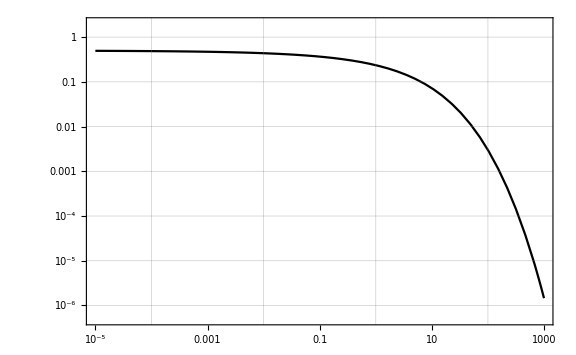

```mathematica
figffo=LogLogPlot[ffoSimp[α],{α, 10^-5,10^3},PlotRange->{Full,{0.5 10^-6,2}},FrameTicks->{{fTicksY,Automatic},{fTicksX,Automatic}},FrameLabel->{MaTeX["\\alpha",Magnification->1.5],MaTeX["f_{\\text{fo}\\ }",Magnification->1.5]},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,PlotStyle->Black,GridLines->Automatic,ImageSize->Large,ImagePadding->{{60,60},{60,30}}]
```

```mathematica
Export["fig_ffo.pdf",figffo]
```

fig_ffo.pdf

#### Draw figure 3: Mass distribution histograms

Abbreviate the mass table and calculate standard deviations of mass for selected values of α1

```mathematica
meanmassfoSimp[α1_,large_]:=2 Sum[ffoSimp[α1 j^2] j^2,{j,1.,large}]
```

```mathematica
meanmasstabSimp=Table[meanmassfoSimp[10.^n,Ceiling[√(10.^(3-n))]],{n,-4.,-1.}];
```

```mathematica
sdmassfoSimp[α1_,large_]:=√(2 Sum[(ffoSimp[α1 j^2]-ffoSimp[α1 j^2]^2)j^4,{j,1.,large}])
```

```mathematica
sdmasstabSimp=Table[sdmassfoSimp[10.^n,Ceiling[√(10.^(3-n))]],{n,-4.,-1.}];
```

Set the number of particles to model

```mathematica
population=10^6;
```

```mathematica
masssample[α1_]:=Block[{dist,j},dist=ConstantArray[0,population];For[j=1.,j≤√(10.^3/α1),j++,
dist=dist+RandomChoice[{1.-ffoSimp[α1 j^2],ffoSimp[α1 j^2]}->{0.,j^2},population]+RandomChoice[{1.-ffoSimp[α1 j^2],ffoSimp[α1 j^2]}->{0.,j^2},population]
];
Return[dist]
]
```

```mathematica
(*sampledata=Table[{10^n,masssample[10.^n]},{n,-4.,-1.}];;*)
```

```mathematica
sampledata=dmwelData["Histograms"];
```

```mathematica
width={100000.,1000.,100.,10.};upper={2.5 10^7,1.2 10^6,60000.,2000.};
glcolour=Purple;glopacity=0.6;masshisto=Table[Histogram[sampledata[[n+5,2]],{Min[sampledata[[n+5,2]]]-0.5,upper[[n+5]]+0.5,width[[n+5]]},"Probability",ChartBaseStyle->{αcolours[[n+5]],Opacity[1.0],EdgeForm[None]},GridLines->{{{meanmasstabSimp[[n+5]]-sdmasstabSimp[[n+5]],{Thick,glcolour,Dashed,Opacity[glopacity]}},{meanmasstabSimp[[n+5]],{Thick,glcolour,Opacity[glopacity]}},{meanmasstabSimp[[n+5]]+sdmasstabSimp[[n+5]],{Thick,glcolour,Dashed,Opacity[glopacity]}}},None},Epilog->Text[histoEpilogs[[n+5]],Scaled[{0.8,.9}]],ImageSize->Medium,BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,Method->{"GridLinesInFront"->True},FrameTicks->histoTicks[[n+5]],PlotRange->{{0,Automatic},Automatic}],{n,-4,-1}];
```

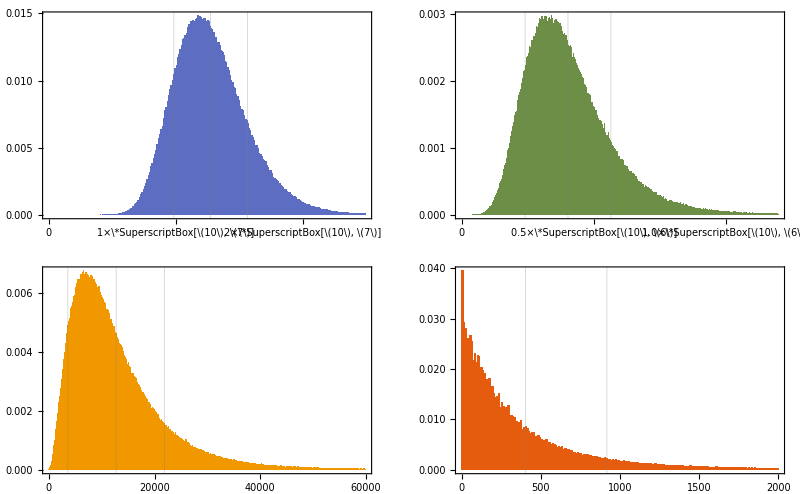

```mathematica
figmasshisto=GraphicsGrid[{{masshisto[[1]],masshisto[[2]]},{masshisto[[3]],masshisto[[4]]}}]
```

```mathematica
Export["fig_masshisto.pdf",figmasshisto]
```

fig_masshisto.pdf

### Section 3.2 Without simplifying assumptions

```mathematica
meanmassfo[α1_,e1_,large_]:=2 e1 Sum[ffo[α1 j^6 hubbleT[e1]/hubbleT[e1 j^2],e1 j^2] j^2,{j,1.,large,Ceiling[large/10000]}]Ceiling[large/10000];ndm0[α1_,e1_]:=ρdm0/meanmassfo[α1,e1,Ceiling[√(10.^3/α1)]]
```

```mathematica
(*massfoTab=Table[{lα1,le1,meanmassfo[10.^lα1,10.^le1 ev,Ceiling[√(10.^(3-lα1))]]},{lα1,-4.,-2.,0.5},{le1,Log10[2.],Log10[2.]+4,0.5}];*)
```

```mathematica
massfoTab=dmwelData["Freezeout masses"];
```

```mathematica
massfoTabLog=Flatten[Table[{massfoTab[[i,j,1]],massfoTab[[i,j,2]],Log10[massfoTab[[i,j,3]]/mev]},{i,Dimensions[massfoTab][[1]]},{j,Dimensions[massfoTab][[2]]}],1];ndm0TabLog=Flatten[Table[{massfoTab[[i,j,1]],massfoTab[[i,j,2]],Log10[Quantity[("Centimeters")^3]ρdm0 /massfoTab[[i,j,3]]]},{i,Dimensions[massfoTab][[1]]},{j,Dimensions[massfoTab][[2]]}],1];
```

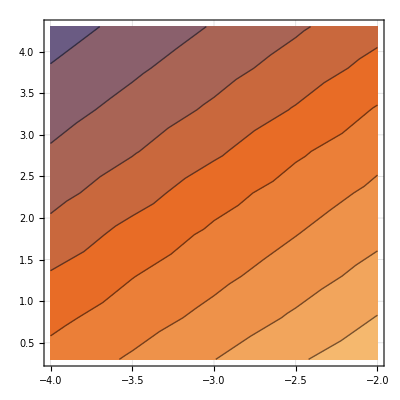

```mathematica
figMass=ListContourPlot[massfoTabLog,BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,GridLines->Automatic,PlotRange->Full,Contours->Range[-2,8,1],ContourShading->Table[ColorData["DarkColorDensityGradient"][1-i],{i,0.,1.,0.1}],FrameLabel->{MaTeX["\\log_{10}\\alpha_1",Magnification->1.3],MaTeX["\\log_{10}E_1",Magnification->1.3]},PlotLegends->BarLegend[Automatic,LegendLayout->"Column",LegendLabel->MaTeX["\\bar{m}_\\text{fo}/\\si{MeV}",Magnification->1.3],LegendMarkerSize->300.,LabelStyle->13],ImagePadding->{{Automatic,10},{Automatic,Automatic}}]
```

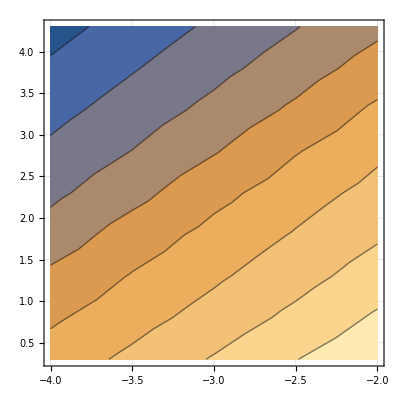

```mathematica
cd=ColorData["M10DefaultDensityGradient"];figNdm=ListContourPlot[ndm0TabLog,Contours->Range[-10,0,1],ColorFunction->"M10DefaultDensityGradient",BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,GridLines->Automatic,PlotRange->Full,FrameLabel->{MaTeX["\\log_{10}\\alpha_1",Magnification->1.3],MaTeX["\\log_{10}E_1",Magnification->1.3]},PlotLegends->BarLegend[Automatic,LegendLayout->"Column",LegendLabel->MaTeX["n_0/\\si{cm^{\\text{-}3}}",Magnification->1.3],LegendMarkerSize->300.,LabelStyle->13],ImagePadding->{{Automatic,10},{Automatic,Automatic}}]
```

```mathematica
Export["fig_Mass.pdf",figMass];Export["fig_Ndm.pdf",figNdm];
```

## Section 4 Cosmological constraints

### Section 4.1 CMB anisotropies

Import DarkAges data  This was made using j_max = 1000,1000,316 - higher j_max does not change the results

```mathematica
parameters=dmwelData["CMB:parameters"];
chiTable=dmwelData["CMB:chi"];
chiHeatTable=Transpose[{chiTable[[1]],chiTable[[2]]}];
chiHIonTable=Transpose[{chiTable[[1]],chiTable[[3]]}];
fcTable=dmwelData["CMB:fc"];
fcHeatTable=Table[Transpose[{fcTable[[n,1]],fcTable[[n,2]]}],{n,1,Length[fcTable]}];
fcHIonTable=Table[Transpose[{fcTable[[n,1]],fcTable[[n,3]]}],{n,1,Length[fcTable]}];
chiHIonFn=Interpolation[chiHIonTable];
chiHeatFn=Interpolation[chiHeatTable];
fcHIonFn=Table[Interpolation[fcHIonTable[[n]]],{n,1,Length[fcTable]}];
fcHeatFn=Table[Interpolation[fcHeatTable[[n]]],{n,1,Length[fcTable]}];
```

Plot figures

```mathematica
(*ndm0TabCMB=Table[ndm0[parameters[[i,1]],parameters[[i,2]]ev],{i,Length[parameters]}];*)
```

```mathematica
ndm0TabCMB=dmwelData["CMB parameter ndm0"];
ndm0Tab={ndm0TabCMB[[2]],ndm0TabCMB[[4]],ndm0TabCMB[[6]]};
```

Note that that fcHIonFn and fcHeatFn are in terms of rate per Log[1+z], hence the need to have the denominator of 1+z

```mathematica
dmepHIon[index_,z_]:=10.^12 UnitConvert[(ndm0TabCMB[[index]]fcHIonFn[[index]][1+z]ev)/(1+z),("Electronvolts")/("Centimeters")^3];dmepHeat[index_,z_]:=10.^12 UnitConvert[(ndm0TabCMB[[index]]fcHeatFn[[index]][1+z]ev)/(1+z),("Electronvolts")/("Centimeters")^3];
annihHIon[z_]:=10.^12 UnitConvert[(pann ρdm0^2(1+z)^2)/hubble[z] chiHIonFn[1+z],("Electronvolts")/("Centimeters")^3];
annihHeat[z_]:=10.^12 UnitConvert[(pann ρdm0^2(1+z)^2)/hubble[z] chiHeatFn[1+z],("Electronvolts")/("Centimeters")^3];
anisotropyFigHIon[index_]:=Plot[{annihHIon[z],dmepHIon[2 index-1,z],dmepHIon[2index,z]},{z,zl,zu},BaseStyle->texStyle,FrameStyle->BlackFrame,PlotStyle->{{Orange,Dashed},{Blue,Opacity[0.25]},Blue},GridLines->glAniso,Filling->{3->{2}},FillingStyle->Opacity[0.1],PlotRange->anisotropyPlotRangeHIon,FrameTicksStyle->anistropyFTSHIon[[index]],FrameTicks->anistropyFTHIon[[index]]]
anisotropyFigHeat[index_]:=Plot[{annihHeat[z],dmepHeat[2 index-1,z],dmepHeat[2index,z]},{z,zl,zu},BaseStyle->texStyle,FrameStyle->BlackFrame,PlotStyle->{{Orange,Dashed},{Blue,Opacity[0.25]},Blue},GridLines->glAniso,Filling->{3->{2}},FillingStyle->Opacity[0.1],PlotRange->anisotropyPlotRangeHeat,FrameTicksStyle->anistropyFTSHeat[[index]],FrameTicks->anistropyFTHeat[[index]],ImageSize->Large,ImagePadding->imPad]
```

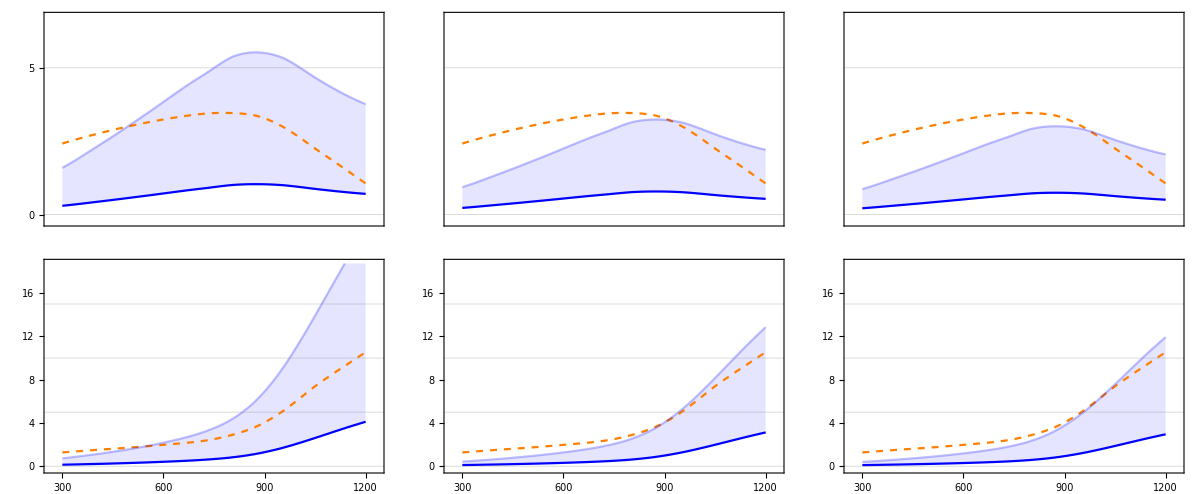

```mathematica
figCMB=GraphicsGrid[{{anisotropyFigHIon[1],anisotropyFigHIon[2],anisotropyFigHIon[3]},{anisotropyFigHeat[1],anisotropyFigHeat[2],anisotropyFigHeat[3]}},Spacings->0]
```

```mathematica
Export["fig_CMB.pdf",figCMB]
```

fig_CMB.pdf

Check that the emissions are decreasing with E_1

```mathematica
figM4HIon=LogPlot[Evaluate[Join[Table[dmepHIon[i,z],{i,7,9}],{dmepHIon[2,z]},Table[dmepHIon[i,z],{i,10,13}]]],{z,zl,zu},BaseStyle->texStyle,FrameStyle->BlackFrame,PlotLabels->Join[Table[ToString[parameters[[i]]],{i,7,9}],{ToString[parameters[[2]]]},Table[ToString[parameters[[i]]],{i,10,13}]],ImageSize->Large]
```

-Graphics-

```mathematica
figM3HIon=LogPlot[Evaluate[Join[Table[dmepHIon[i,z],{i,14,17}],{dmepHIon[4,z]},Table[dmepHIon[i,z],{i,18,20}]]],{z,zl,zu},BaseStyle->texStyle,FrameStyle->BlackFrame,PlotLabels->Join[Table[ToString[parameters[[i]]],{i,14,17}],{ToString[parameters[[4]]]},Table[ToString[parameters[[i]]],{i,18,20}]],ImageSize->Large]
```

-Graphics-

```mathematica
figM2HIon=LogPlot[Evaluate[Join[Table[dmepHIon[i,z],{i,21,25}],{dmepHIon[6,z]},Table[dmepHIon[i,z],{i,26,27}]]],{z,zl,zu},BaseStyle->texStyle,FrameStyle->BlackFrame,PlotLabels->Join[Table[ToString[parameters[[i]]],{i,21,25}],{ToString[parameters[[6]]]},Table[ToString[parameters[[i]]],{i,26,27}]],ImageSize->Large]
```

-Graphics-

```mathematica
figM4Heat=LogPlot[Evaluate[Join[Table[dmepHeat[i,z],{i,7,9}],{dmepHeat[2,z]},Table[dmepHeat[i,z],{i,10,13}]]],{z,zl,zu},BaseStyle->texStyle,FrameStyle->BlackFrame,PlotLabels->Join[Table[ToString[parameters[[i]]],{i,7,9}],{ToString[parameters[[2]]]},Table[ToString[parameters[[i]]],{i,10,13}]],ImageSize->Large]
```

-Graphics-

```mathematica
figM3Heat=LogPlot[Evaluate[Join[Table[dmepHeat[i,z],{i,14,17}],{dmepHeat[4,z]},Table[dmepHeat[i,z],{i,18,20}]]],{z,zl,zu},BaseStyle->texStyle,FrameStyle->BlackFrame,PlotLabels->Join[Table[ToString[parameters[[i]]],{i,14,17}],{ToString[parameters[[4]]]},Table[ToString[parameters[[i]]],{i,18,20}]],ImageSize->Large]
```

-Graphics-

```mathematica
figM2Heat=LogPlot[Evaluate[Join[Table[dmepHeat[i,z],{i,21,25}],{dmepHeat[6,z]},Table[dmepHeat[i,z],{i,26,27}]]],{z,zl,zu},BaseStyle->texStyle,FrameStyle->BlackFrame,PlotLabels->Join[Table[ToString[parameters[[i]]],{i,21,25}],{ToString[parameters[[6]]]},Table[ToString[parameters[[i]]],{i,26,27}]],ImageSize->Large]
```

-Graphics-

### Section 4.2 CMB energy density and spectrum

```mathematica
photonenergydensityboth[temp_]:=(π^2 temp^4)/(15 hbar^3 c^3)
```

#### Calculate the relative reduction in CMB energy density at 10 MeV for α1=10^-3, and E1 at the reference energy

```mathematica
ργdmintegrand[α1_,e1_,Tdown_,Tup_]:=-(2α1 hubbleT[e1])/e1^3 NIntegrate[(T^2 gstarSdenom[T])/hubbleT[T](gstarS0/gstarS[T/ev])^(1./3.)Sum[((Exp[-(e1 j^2)/T]-f[α1 j^6 hubbleT[e1]/hubbleT[e1 j^2],e1 j^2,T](1+Exp[-(e1 j^2)/T]))/(1-Exp[-(e1 j^2)/T])),{j,Ceiling[√(10.^3/α1)]}],{T,Tdown,Tup},PrecisionGoal->4]
```

```mathematica
ργdmintegrandrel[α1_,e1_,Tdown_,Tup_]:=-(2α1 hubbleT[e1])/e1^3 ev^3 NIntegrate[(Exp[3 lT]gstarSdenom[Exp[lT]ev])/hubbleT[Exp[lT]ev](gstarS0/gstarS[Exp[lT]])^(1./3.)Sum[((Exp[-(e1 j^2)/(Exp[lT]ev)]-f[α1 j^6 hubbleT[e1]/hubbleT[e1 j^2],e1 j^2,Exp[lT]ev](1+Exp[-(e1 j^2)/(Exp[lT]ev)]))/(1-Exp[-(e1 j^2)/(Exp[lT]ev)])),{j,Ceiling[√(10.^3/α1)]}],{lT,Log[Tdown/ev],Log[Tup/ev]},PrecisionGoal->4]
```

```mathematica
ndm0Select[α1_]:=Which[α1==10.^-4,ndm0Tab[[1]],α1==10.^-3,ndm0Tab[[2]],α1==10.^-2,ndm0Tab[[3]],True,"Error"]
```

```mathematica
relReduction[α1_]:=Module[{ndm0Selected,e1},ndm0Selected=ndm0Select[α1];e1=refev α1 10.^3;(ndm0Selected tcmbinev)/photonenergydensityboth[tcmbinev] ργdmintegrandrel[α1,e1,tcmbinev,10.^7 ev]]
```

```mathematica
relRedTab=Table[relReduction[10.^lα1],{lα1,-4.,-2.}];pSF[relRedTab,1]
```

{ 9.×10^-5, 7.×10^-5, 7.×10^-5}

#### Calculating μ (to speed up, only works for selected α1, so can use pre-calculated ndm0). The calculation still takes several minutes

```mathematica
specdistμ[α1_]:=Module[{ndm0Selected,e1},ndm0Selected=ndm0Select[α1];e1=refev α1 10.^3;1.401((ndm0Selected tcmbinev)/photonenergydensityboth[tcmbinev])ργdmintegrand[α1,e1,10.ev,500.ev]]
```

```mathematica
pSF[μresults=Table[specdistμ[10.^lα1],{lα1,-4.,-2.}],1]
```

{ 2.×10^-7, 1.×10^-7, 1.×10^-7}

#### Calculating y (to speed up, only works for selected α1, so can use pre-calculated ndm0). The calculation still takes several minutes

```mathematica
specdisty[α1_]:=Module[{ndm0Selected,e1},ndm0Selected=ndm0Select[α1];e1=refev α1 10.^3;1/4((ndm0Selected tcmbinev)/photonenergydensityboth[tcmbinev])ργdmintegrand[α1,e1,temprecomb,10.ev]]
```

```mathematica
pSF[yresults=Table[specdisty[10.^lα1],{lα1,-4.,-2.}],1]
```

{ 5.×10^-10, 4.×10^-10, 3.×10^-10}

#### Calculate the DMWEL emission spectrum at the present day (to speed up, only works for selected α1, so can use pre-calculated ndm0).

Emissions strength (the Quiet switches off apparent unit compatibility errors when the Sum vanishes)

```mathematica
emStrength[α1_,ν_]:=Module[{ndm0Selected,e1},ndm0Selected=Which[α1==10.^-4,ndm0Tab[[1]],α1==10.^-3,ndm0Tab[[2]],α1==10.^-2,ndm0Tab[[3]],True,"Error"];e1=refev α1 10^3;If[(2 π hbar ν)<(e1 tcmbinev)/temprecomb,Quantity[0,("Nanowatts")/("Meters")^2],Quiet[UnitConvert[(c ndm0Selected tcmbinev^4 α1 hubbleT[e1])/(2 π (2 π hbar ν)^3)Sum[(j^6 ffo[α1 j^6 hubbleT[e1]/hubbleT[e1 j^2],e1 j^2])/hubbleT[(e1 j^2 tcmbinev)/(2 π hbar ν)],{j, Ceiling[√((2 π hbar ν)/e1)],Min[3000,Floor[√((temprecomb(2 π hbar ν))/(tcmbinev e1))]]}],("Nanowatts")/("Meters")^2]]]]
```

Calculate the emissions strengths for the minimum energies compatible with anisotropy constraints

```mathematica
emStrengthTable=Table[{Quantity[10.^lλ,"Meters"],emStrength[10.^lα1,c/Quantity[10.^lλ,"Meters"]]},{lα1,-4.,-2.},{lλ,-18.,2.}];
```

Data from Cooray (2016)

```mathematica
CoorayPreTable={{-17,1.2 10^-4},{-16,4. 10^-4},{-15,9. 10^-4},{-14,2. 10^-3},{-13,2. 10^-3},{-12,6. 10^-3},{-11,4. 10^-2},{-10,6. 10^-2},{-9,2. 10^-2},{Log10[3.8 10^-9],2.5 10^-2},{-7,2. 10^0},{-6,1.3 10^1},{-5,1.3 10^0},{-4,8. 10^0},{-3,2. 10^0},{-2,3. 10^1}};CoorayTable=Table[{Quantity[10.^CoorayPreTable[[i,1]],"Meters"],Quantity[CoorayPreTable[[i,2]],("Nanowatts")/("Meters")^2]},{i,Length[CoorayPreTable]}];
```

Plot the emissions spectrum

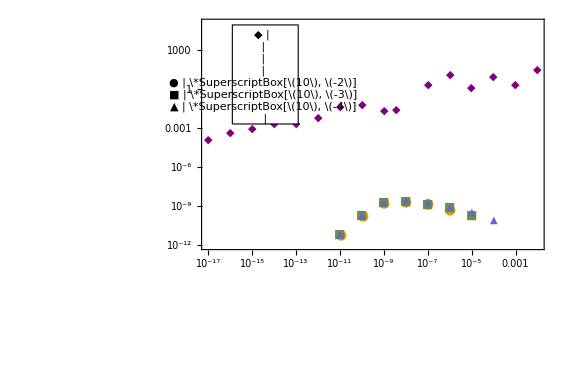

```mathematica
figEmissionsSpectrum=ListLogLogPlot[{emStrengthTable[[3]],emStrengthTable[[2]],emStrengthTable[[1]],CoorayTable},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,FrameLabel->{MaTeX["\\sfrac{\\lambda\\,}{\\si{m}}",Magnification->1.75],MaTeX["\\sfrac{E\\,I}{\\si{nW.m^{\\text{-}2}.sr^{\\text{-}1}}}",Magnification->1.75]},PlotRange->{{10.^-17,10.^-2},{10.^-12,10.^5}},AspectRatio->2/3,PlotMarkers->{"●","■","▲","◆"},PlotStyle->{RGBColor[0.945109, 0.593901, 0.],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.365248, 0.427802, 0.758297],{Bold,Purple}},ImageSize->Large,GridLines->{10^Range[-15,-3,3],Automatic},FrameTicks->{{emissionsSpectrum,Automatic},{emissionsSpectrum,Automatic}},Epilog->{{EdgeForm[Black],White,Rectangle[{Log[10^-15.9],Log[10^-2.7]},{Log[10^-12.9],Log[10^4.9]}]},Inset[Grid[{{Style["StyleBox[\"◆\",FontSize->12]",Purple],MaTeX["\\text{EBL}"]},{"",""},{MaTeX["\\text{DMWEL}",Magnification->1.],SpanFromLeft},{"",MaTeX["\\alpha_1",Magnification->1.25]},{Style["StyleBox[\"●\",FontSize->14]",RGBColor[0.945109, 0.593901, 0.]],"\*SuperscriptBox[\(10\), \(-2\)]"},{Style["StyleBox[\"■\",FontSize->12]",RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023]], "\*SuperscriptBox[\(10\), \(-3\)]"},{Style["StyleBox[\"▲\",FontSize->10]",RGBColor[0.365248, 0.427802, 0.758297]],"\*SuperscriptBox[\(10\), \(-4\)]"},{"",SpanFromLeft}},Alignment->Center,Spacings->{0,0.2}],Scaled[{0.18,0.75}]]}]
```

```mathematica
Export["fig_Emissions_Spectrum.pdf",figEmissionsSpectrum]
```

fig_Emissions_Spectrum.pdf

The following are examples showing higher energies E_1 gives lower emissions strength near the DMWEL peak

This is for E1 very slightly higher than the reference values

```mathematica
emStrengthHigher[α1_,e1_,ndm0Selected_,ν_]:=If[(2 π hbar ν)<(e1 tcmbinev)/temprecomb,Quantity[0,("Nanowatts")/("Meters")^2],Quiet[UnitConvert[(c ndm0Selected tcmbinev^4 α1 hubbleT[e1])/(2 π (2 π hbar ν)^3)Sum[(j^6 ffo[α1 j^6 hubbleT[e1]/hubbleT[e1 j^2],e1 j^2])/hubbleT[(e1 j^2 tcmbinev)/(2 π hbar ν)],{j, Ceiling[√((2 π hbar ν)/e1)],Min[3000,Floor[√((temprecomb(2 π hbar ν))/(tcmbinev e1))]]}],("Nanowatts")/("Meters")^2]]]
```

```mathematica
With[{α1=10.^-3,e1=25.ev},ndm0Selected=ndm0[α1,e1];emStrengthTableM3Higher=Table[{Quantity[10.^lλ,"Meters"],emStrengthHigher[α1,e1,ndm0Selected,c/Quantity[10.^lλ,"Meters"]]},{lλ,-18.,2.}]];
```

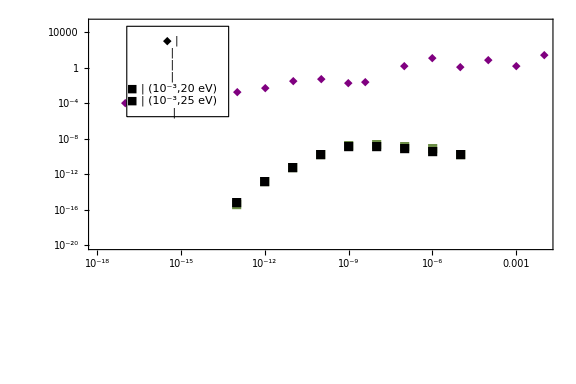

```mathematica
figEmissionsSpectrumM3Higher=ListLogLogPlot[{emStrengthTable[[2]],emStrengthTableM3Higher,CoorayTable},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,FrameLabel->{MaTeX["\\sfrac{\\lambda\\,}{\\si{m}}",Magnification->1.75],MaTeX["\\sfrac{\\mathcal{E}}{\\si{nW.m^{\\text{-}2}}}",Magnification->1.75]},PlotRange->{{10.^-18,10.^-2},{10.^-20,10.^5}},AspectRatio->2/3,PlotMarkers->{"■","■","◆"},PlotStyle->{RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],Black,{Bold,Purple}},ImageSize->Large,GridLines->Automatic,Epilog->{{EdgeForm[Black],White,Rectangle[{Log[10^-16.95],Log[10^-5.5]},{Log[10^-13.3],Log[10^4.7]}]},Inset[Grid[{{Style["StyleBox[\"◆\",FontSize->12]",Purple],MaTeX["\\text{EBL}"]},{"",""},{MaTeX["\\text{DMWEL}",Magnification->1.],SpanFromLeft},{"",MaTeX["(\\alpha_1,E_1)",Magnification->1.25]},{Style["StyleBox[\"■\",FontSize->12]",RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023]], "(10^-3,20 eV)"},{Style["StyleBox[\"■\",FontSize->12]",Black],"(10^-3,25 eV)"},{"",SpanFromLeft}},Alignment->Center,Spacings->{0,0.2}],Scaled[{0.18,0.75}]]}]
```

This is for E1 more than slightly higher than the reference values

```mathematica
With[{α1=10.^-3,e1=2000.ev},ndm0Selected=ndm0[α1,e1];emStrengthTableM3Higher2=Table[{Quantity[10.^lλ,"Meters"],emStrengthHigher[α1,e1,ndm0Selected,c/Quantity[10.^lλ,"Meters"]]},{lλ,-16.,2.}]];
```

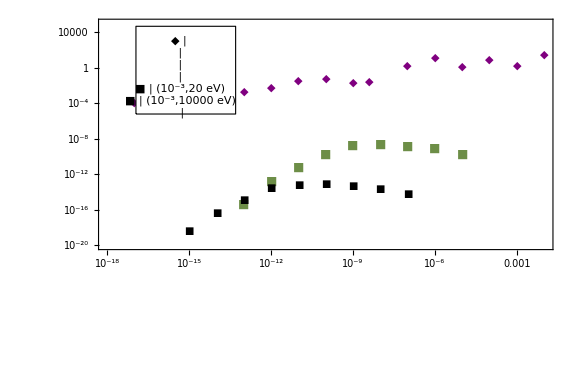

```mathematica
figEmissionsSpectrumM3Higher2=ListLogLogPlot[{emStrengthTable[[2]],emStrengthTableM3Higher2,CoorayTable},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,FrameLabel->{MaTeX["\\sfrac{\\lambda\\,}{\\si{m}}",Magnification->1.75],MaTeX["\\sfrac{\\mathcal{E}}{\\si{nW.m^{\\text{-}2}}}",Magnification->1.75]},PlotRange->{{10.^-18,10.^-2},{10.^-20,10.^5}},AspectRatio->2/3,PlotMarkers->{"■","■","◆"},PlotStyle->{RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],Black,{Bold,Purple}},ImageSize->Large,GridLines->Automatic,Epilog->{{EdgeForm[Black],White,Rectangle[{Log[10^-16.95],Log[10^-5.2]},{Log[10^-13.3],Log[10^4.7]}]},Inset[Grid[{{Style["StyleBox[\"◆\",FontSize->12]",Purple],MaTeX["\\text{EBL}"]},{"",""},{MaTeX["\\text{DMWEL}",Magnification->1.],SpanFromLeft},{"",MaTeX["(\\alpha_1,E_1)",Magnification->1.25]},{Style["StyleBox[\"■\",FontSize->12]",RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023]], "(10^-3,20 eV)"},{Style["StyleBox[\"■\",FontSize->10]",Black],"(10^-3,10000 eV)"},{"",SpanFromLeft}},Alignment->Center,Spacings->{0,0.2}],Scaled[{0.18,0.75}]]}]
```

### Section 4.3 Post-BBN photodissociation of nuclei

#### Forestell+ spectra

Set up, and import data

```mathematica
EXgrid={10.^6.,2. 10.^6.,3. 10.^6.,5. 10.^6.,10.^7.,3. 10.^7.,10.^8.,10.^8.75};lEXgrid=Length[EXgrid];Tgrid={0.1,1.,10.,100.,10^2.8,10^3.,10^3.2,10^3.4,10^3.6,10^3.8,10^4.};
lTgrid=Length[Tgrid];
Ebottom=1. 10^6;
enArray=dmwelData["fForestell:en"];
fγArray=dmwelData["fForestell:fgamma"];
```

Do interpolation

```mathematica
fγInterpList=Union[Flatten[Table[{{Log[EXgrid[[EXindex]]],Log[Tgrid[[Tindex]]],Log[enArray[[EXindex,Tindex,step]]]},Log[fγArray[[EXindex,Tindex,step]]]},{EXindex,2,lEXgrid},{Tindex,1,lTgrid},{step,1,Length[enArray[[EXindex,Tindex]]]}],2]];
```

```mathematica
fγInterp=Interpolation[fγInterpList,InterpolationOrder->1]
```

InterpolatingFunction[{{14.5087, 20.1476}, {-2.30259, 9.21034}, {13.8155, 20.1476}}, <>]

```mathematica
fForestell[EX_,T_,En_]:=If[10.^6≤En≤EX,Exp[fγInterp[Log[EX],Log[T],Log[En]]],0.]
```

#### The reaction matrix for photodissociation

eqnMatrixpreFinal does nuclides in the order X, D, T, 3He, 4He, 6Li, 7Li, 7Be. X = p or n or A3 is only used as a sink

```mathematica
eqnMatrixpreFinal[EX_,T_]:=Normal[SparseArray[{{2,1}->σDpfn[EX,T],{3,1}->σTnfn[EX,T],{4,1}->σ3Hepfn[EX,T],{6,1}->σ6Li3Afn[EX,T],{3,2}->σTDfn[EX,T],{4,2}->σ3HeDfn[EX,T],{5,3}->σ4HeTfn[EX,T],{5,4}->σ4He3Hefn[EX,T],{5,2}->2σ4HeDR1fn[EX,T]+σ4HeDR2fn[EX,T],{6,5}->σ6Li4Hefn[EX,T],{7,3}->σ7LiT4Hefn[EX,T],{7,5}->σ7LiT4Hefn[EX,T]+σ7Li4Hefn[EX,T],{7,6}->σ7Li6Lifn[EX,T],{8,4}->σ7Be3He4Hefn[EX,T],{8,5}->σ7Be3He4Hefn[EX,T]+σ7Be4Hefn[EX,T],{8,6}->σ7Be6Lifn[EX,T]},{8,8}]]
```

eqnMatrixpreInitial omits the sink

```mathematica
eqnMatrixpreInitial[EX_,T_]:=DiagonalMatrix[{σDpfn[EX,T],σTnfn[EX,T]+σTDfn[EX,T],σ3Hepfn[EX,T]+σ3HeDfn[EX,T],σ4HeTfn[EX,T]+σ4He3Hefn[EX,T]+σ4HeDR1fn[EX,T]+σ4HeDR2fn[EX,T],σ6Li3Afn[EX,T]+σ6Li4Hefn[EX,T],σ7LiT4Hefn[EX,T]+σ7Li4Hefn[EX,T]+σ7Li6Lifn[EX,T],σ7Be3He4Hefn[EX,T]+σ7Be4Hefn[EX,T]+σ7Be6Lifn[EX,T]}]
```

```mathematica
eqnMatrix[EX_,T_]:=-eqnMatrixpreInitial[EX,T]+Table[eqnMatrixpreFinal[EX,T][[j,i]],{i,2,8},{j,2,8}]
```

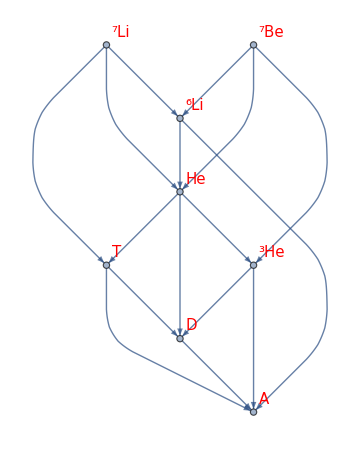

```mathematica
wag=WeightedAdjacencyGraph[Table[If[eqnMatrixpreFinal[EX,T][[i,j]]===0,∞,eqnMatrixpreFinal[EX,T][[i,j]]],{i,1,8},{j,1,8}],EdgeLabels->Placed["EdgeWeight",Tooltip],VertexLabels->{1->"A",2->"D",3->"T",4->"^3He",5->"He",6->"^6Li",7->"^7Li",8->"^7Be"},VertexLabelStyle->Directive[Red,15],GraphLayout->"LayeredDigraphEmbedding",ImageSize->Medium]
```

#### Create the cross-section and related functions

Don’t need to account for the 3A as T or 3He because 6Li is so much less abundant

```mathematica
EDpth=2.224573 10^6;σDp[Eγ_]:=If[Eγ>EDpth,18.75 mbtoev(((√(EDpth(Eγ-EDpth)))/Eγ)^3+0.007947((√(EDpth(Eγ-EDpth)))/Eγ)^2 (√EDpth-√0.037)^2/(Eγ-(EDpth-0.037))),0.];σstd[Eth_,coeff_,lpower_,rpower_,Eγ_]:=If[Eγ>Eth,coeff mbtoev((Eth^lpower(Eγ-Eth)^rpower)/Eγ^(lpower+rpower)),0.];ETDth=6.257248 10^6;σTD[Eγ_]:=σstd[ETDth,9.8,1.95,1.65,Eγ];ETnth=8.481821 10^6;σTn[Eγ_]:=σstd[ETnth,26.0,2.6,2.3,Eγ];E3HeDth=5.493485 10^6;σ3HeD[Eγ_]:=σstd[E3HeDth,8.88,1.75,1.65,Eγ];E3Hepth=7.718058 10^6;σ3Hep[Eγ_]:=σstd[E3Hepth,16.7,1.95,2.3,Eγ];E4HeTth=19.813852 10^6;σ4HeT[Eγ_]:=σstd[E4HeTth,19.5,3.5,1.0,Eγ];E4He3Heth=20.577615 10^6;σ4He3He[Eγ_]:=σstd[E4He3Heth,17.1,3.5,1.0,Eγ];E4HeDR1th=23.846527 10^6;E4HeDR2th=26.0711 10^6;σ4HeDR1[Eγ_]:=σstd[E4HeDR1th,10.7,10.2,3.4,Eγ];σ4HeDR2[Eγ_]:=σstd[E4HeDR2th,21.7,4.0,3.0,Eγ];E6Li4Heth=3.698892 10^6;σ6Li4He[Eγ_]:=σstd[E6Li4Heth,104,2.3,4.7,Eγ];E6Li3Ath=15.794685 10^6;σ6Li3A[Eγ_]:=σstd[E6Li3Ath,38.1,3.0,2.0,Eγ](3.7 Exp[-1/2((Eγ-19.0 10^6)/(3.5 10^6))^2]+2.75Exp[-1/2((Eγ-30.0 10^6)/(3.0 10^6))^2]+2.2 Exp[-1/2((Eγ-43.0 10^6)/(5.0 10^6))^2]);E7Li6Lith=7.249962 10^6;σ7Li6Li[Eγ_]:=σstd[E7Li6Lith,0.176,1.51,0.49,Eγ]+σstd[E7Li6Lith,1205,5.5,5.0,Eγ]+If[Eγ>E7Li6Lith,(0.06 mbtoev)/(1+((((Eγ-E7Li6Lith)/10.^6)-7.46)/0.188)^2),0.];E7Li4Heth=10.948850 10^6;σ7Li4He[Eγ_]:=σstd[E7Li4Heth,122,4.0,3.0,Eγ];E7Be6Lith=5.605794 10^6;σ7Be6Li[Eγ_]:=σstd[E7Be6Lith,32.6,10.0,2.0,Eγ]+σstd[E7Be6Lith,2.27 10^6,8.8335,13.0,Eγ];E7Be4Heth=9.30468 10^6;σ7Be4He[Eγ_]:=σstd[E7Be4Heth,133.,4.0,3.0,Eγ];
```

From  Effects of Long-lived 10 MeV Scale Sterile Neutrino on Primordial Elemental
Abundances and Effective Neutrino Number, Ishida+, 2015

```mathematica
E7LiT4Heth=2.467032 10^6;σ7LiT4He[Eγ_]:=Which[Eγ>E7LiT4Heth+10.^6,(48.1 10^12 mbtoev)/Eγ^2 Exp[(-2.60 10^3)/(√(Eγ-E7LiT4Heth))],Eγ>E7LiT4Heth,((80.3 10^12 mbtoev)/Eγ^2)Exp[(-2.60 10^3)/(√(Eγ-E7LiT4Heth))]Exp[-2.056 (Eγ-E7LiT4Heth)/10.^6](1.+2.2875((Eγ-E7LiT4Heth)/10.^6)^2-1.1798((Eγ-E7LiT4Heth)/10.^6)^3+2.5279((Eγ-E7LiT4Heth)/10.^6)^4),True,0.];Q7Be={E7Be3He4Heth=1.586627 10^6,1.1570 10^6};s0={0.406,0.163};s2={0.007,0.004};ai=-0.134;finestructureα=7.29735257 10^-3;massunit=931.4940954 10^6;mass3He=3.0160293massunit-2masselectron;mass4He=4.00260massunit-2masselectron;EG=2(mass3He mass4He)/(mass3He+mass4He)(4π finestructureα)^2;σ7Be3He4He[Eγ_]:=If[Eγ>Q7Be[[1]],(801  10^12 mbtoev)/Eγ^2 Exp[-(5.19 10^3)/(√(Eγ-Q7Be[[1]]))]Sum[Q7Be[[i+1]]/(Eγ-Q7Be[[1]]+Q7Be[[i+1]])(s0[[i+1]](1+ai (Eγ-Q7Be[[1]])/10.^6)^2+s2[[i+1]](1+4 π^2 (Eγ-Q7Be[[1]])/EG)(1+16 π^2 (Eγ-Q7Be[[1]])/EG)),{i,0,1}],0.]
```

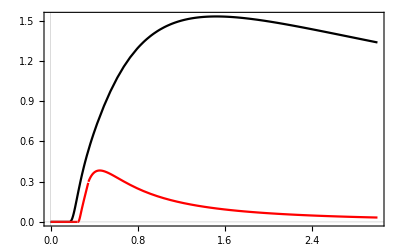

```mathematica
Plot[{σ7Be3He4He[Eγ]/mbtoev,σ7LiT4He[Eγ]/mbtoev},{Eγ,0,30. 10^6},PlotRange->Full,PlotStyle->{Black,Red}]
```

Ignore secondary production

#### Create the functions related via Forestell+ to cross-sections

```mathematica
(*mult=Exp[0.1];*)
```

```mathematica
(*σDpArray=Table[{{lnEX,lnT},Log[NIntegrate[σDp[En]fForestell[Exp[lnEX],Exp[lnT],En],{En,EDpth,Exp[lnEX]}]]},{lnEX,Log[EDpth]+0.1,8.75 Log[10.],0.1},{lnT,Log[0.1],Log[10.^4],1}];σDpArraylow=Table[{σDpArray[[1,Tindex2,1,2]],σDpArray[[1,Tindex2,2]]},{Tindex2,1,Length[σDpArray[[1]]]}];σDpfnpre=Interpolation[Flatten[σDpArray,1]];σDpfnprelow=Interpolation[σDpArraylow];Clear[σDpfn];σDpfn[EX_,T_]:=Which[EX≥mult EDpth,Exp[σDpfnpre[Log[EX],Log[T]]],EX>EDpth,((EX-EDpth)Exp[σDpfnprelow[Log[T]]])/((mult-1)EDpth),True,0.]+σDp[EX]/Γγ[EX,T]*)
```

```mathematica
(*σTDArray=Table[{{lnEX,lnT},Log[NIntegrate[σTD[En]fForestell[Exp[lnEX],Exp[lnT],En],{En,ETDth,Exp[lnEX]}]]},{lnEX,Log[ETDth]+0.1,8.75 Log[10.],0.1},{lnT,Log[0.1],Log[10.^4],1}];σTDArraylow=Table[{σTDArray[[1,Tindex2,1,2]],σTDArray[[1,Tindex2,2]]},{Tindex2,1,Length[σTDArray[[1]]]}];σTDfnpre=Interpolation[Flatten[σTDArray,1]];σTDfnprelow=Interpolation[σTDArraylow];Clear[σTDfn];σTDfn[EX_,T_]:=Which[EX≥mult ETDth,Exp[σTDfnpre[Log[EX],Log[T]]],EX>ETDth,((EX-ETDth)Exp[σTDfnprelow[Log[T]]])/((mult-1)ETDth),True,0.]+σTD[EX]/Γγ[EX,T]*)
```

```mathematica
(*σTnArray=Table[{{lnEX,lnT},Log[NIntegrate[σTn[En]fForestell[Exp[lnEX],Exp[lnT],En],{En,ETnth,Exp[lnEX]}]]},{lnEX,Log[ETnth]+0.1,8.75 Log[10.],0.1},{lnT,Log[0.1],Log[10.^4],1}];σTnArraylow=Table[{σTnArray[[1,Tindex2,1,2]],σTnArray[[1,Tindex2,2]]},{Tindex2,1,Length[σTnArray[[1]]]}];σTnfnpre=Interpolation[Flatten[σTnArray,1]];σTnfnprelow=Interpolation[σTnArraylow];Clear[σTnfn];σTnfn[EX_,T_]:=Which[EX≥mult ETnth,Exp[σTnfnpre[Log[EX],Log[T]]],EX>ETnth,((EX-ETnth)Exp[σTnfnprelow[Log[T]]])/((mult-1)ETnth),True,0.]+σTn[EX]/Γγ[EX,T]*)
```

```mathematica
(*σ3HeDArray=Table[{{lnEX,lnT},Log[NIntegrate[σ3HeD[En]fForestell[Exp[lnEX],Exp[lnT],En],{En,E3HeDth,Exp[lnEX]}]]},{lnEX,Log[E3HeDth]+0.1,8.75 Log[10.],0.1},{lnT,Log[0.1],Log[10.^4],1}];σ3HeDArraylow=Table[{σ3HeDArray[[1,Tindex2,1,2]],σ3HeDArray[[1,Tindex2,2]]},{Tindex2,1,Length[σ3HeDArray[[1]]]}];σ3HeDfnpre=Interpolation[Flatten[σ3HeDArray,1]];σ3HeDfnprelow=Interpolation[σ3HeDArraylow];Clear[σ3HeDfn];σ3HeDfn[EX_,T_]:=Which[EX≥mult E3HeDth,Exp[σ3HeDfnpre[Log[EX],Log[T]]],EX>E3HeDth,((EX-E3HeDth)Exp[σ3HeDfnprelow[Log[T]]])/((mult-1)E3HeDth),True,0.]+σ3HeD[EX]/Γγ[EX,T]*)
```

```mathematica
(*σ3HepArray=Table[{{lnEX,lnT},Log[NIntegrate[σ3Hep[En]fForestell[Exp[lnEX],Exp[lnT],En],{En,E3Hepth,Exp[lnEX]}]]},{lnEX,Log[E3Hepth]+0.1,8.75 Log[10.],0.1},{lnT,Log[0.1],Log[10.^4],1}];σ3HepArraylow=Table[{σ3HepArray[[1,Tindex2,1,2]],σ3HepArray[[1,Tindex2,2]]},{Tindex2,1,Length[σ3HepArray[[1]]]}];σ3Hepfnpre=Interpolation[Flatten[σ3HepArray,1]];σ3Hepfnprelow=Interpolation[σ3HepArraylow];Clear[σ3Hepfn];σ3Hepfn[EX_,T_]:=Which[EX≥mult E3Hepth,Exp[σ3Hepfnpre[Log[EX],Log[T]]],EX>E3Hepth,((EX-E3Hepth)Exp[σ3Hepfnprelow[Log[T]]])/((mult-1)E3Hepth),True,0.]+σ3Hep[EX]/Γγ[EX,T]*)
```

```mathematica
(*σ4HeTArray=Table[{{lnEX,lnT},Log[NIntegrate[σ4HeT[En]fForestell[Exp[lnEX],Exp[lnT],En],{En,E4HeTth,Exp[lnEX]}]]},{lnEX,Log[E4HeTth]+0.1,8.75 Log[10.],0.1},{lnT,Log[0.1],Log[10.^4],1}];σ4HeTArraylow=Table[{σ4HeTArray[[1,Tindex2,1,2]],σ4HeTArray[[1,Tindex2,2]]},{Tindex2,1,Length[σ4HeTArray[[1]]]}];σ4HeTfnpre=Interpolation[Flatten[σ4HeTArray,1]];σ4HeTfnprelow=Interpolation[σ4HeTArraylow];Clear[σ4HeTfn];σ4HeTfn[EX_,T_]:=Which[EX≥mult E4HeTth,Exp[σ4HeTfnpre[Log[EX],Log[T]]],EX>E4HeTth,((EX-E4HeTth)Exp[σ4HeTfnprelow[Log[T]]])/((mult-1)E4HeTth),True,0.]+σ4HeT[EX]/Γγ[EX,T]*)
```

```mathematica
(*σ4He3HeArray=Table[{{lnEX,lnT},Log[NIntegrate[σ4He3He[En]fForestell[Exp[lnEX],Exp[lnT],En],{En,E4He3Heth,Exp[lnEX]}]]},{lnEX,Log[E4He3Heth]+0.1,8.75 Log[10.],0.1},{lnT,Log[0.1],Log[10.^4],1}];σ4He3HeArraylow=Table[{σ4He3HeArray[[1,Tindex2,1,2]],σ4He3HeArray[[1,Tindex2,2]]},{Tindex2,1,Length[σ4He3HeArray[[1]]]}];σ4He3Hefnpre=Interpolation[Flatten[σ4He3HeArray,1]];σ4He3Hefnprelow=Interpolation[σ4He3HeArraylow];Clear[σ4He3Hefn];σ4He3Hefn[EX_,T_]:=Which[EX≥mult E4He3Heth,Exp[σ4He3Hefnpre[Log[EX],Log[T]]],EX>E4He3Heth,((EX-E4He3Heth)Exp[σ4He3Hefnprelow[Log[T]]])/((mult-1)E4He3Heth),True,0.]+σ4He3He[EX]/Γγ[EX,T]*)
```

```mathematica
(*σ4HeDR1Array=Table[{{lnEX,lnT},Log[NIntegrate[σ4HeDR1[En]fForestell[Exp[lnEX],Exp[lnT],En],{En,E4HeDR1th,Exp[lnEX]}]]},{lnEX,Log[E4HeDR1th]+0.1,8.75 Log[10.],0.1},{lnT,Log[0.1],Log[10.^4],1}];σ4HeDR1Arraylow=Table[{σ4HeDR1Array[[1,Tindex2,1,2]],σ4HeDR1Array[[1,Tindex2,2]]},{Tindex2,1,Length[σ4HeDR1Array[[1]]]}];σ4HeDR1fnpre=Interpolation[Flatten[σ4HeDR1Array,1]];σ4HeDR1fnprelow=Interpolation[σ4HeDR1Arraylow];Clear[σ4HeDR1fn];σ4HeDR1fn[EX_,T_]:=Which[EX≥mult E4HeDR1th,Exp[σ4HeDR1fnpre[Log[EX],Log[T]]],EX>E4HeDR1th,((EX-E4HeDR1th)Exp[σ4HeDR1fnprelow[Log[T]]])/((mult-1)E4HeDR1th),True,0.]+σ4HeDR1[EX]/Γγ[EX,T]*)
```

```mathematica
(*σ4HeDR2Array=Table[{{lnEX,lnT},Log[NIntegrate[σ4HeDR2[En]fForestell[Exp[lnEX],Exp[lnT],En],{En,E4HeDR2th,Exp[lnEX]}]]},{lnEX,Log[E4HeDR2th]+0.1,8.75 Log[10.],0.1},{lnT,Log[0.1],Log[10.^4],1}];σ4HeDR2Arraylow=Table[{σ4HeDR2Array[[1,Tindex2,1,2]],σ4HeDR2Array[[1,Tindex2,2]]},{Tindex2,1,Length[σ4HeDR2Array[[1]]]}];σ4HeDR2fnpre=Interpolation[Flatten[σ4HeDR2Array,1]];σ4HeDR2fnprelow=Interpolation[σ4HeDR2Arraylow];Clear[σ4HeDR2fn];σ4HeDR2fn[EX_,T_]:=Which[EX≥mult E4HeDR2th,Exp[σ4HeDR2fnpre[Log[EX],Log[T]]],EX>E4HeDR2th,((EX-E4HeDR2th)Exp[σ4HeDR2fnprelow[Log[T]]])/((mult-1)E4HeDR2th),True,0.]+σ4HeDR2[EX]/Γγ[EX,T]*)
```

```mathematica
(*σ6Li4HeArray=Table[{{lnEX,lnT},Log[NIntegrate[σ6Li4He[En]fForestell[Exp[lnEX],Exp[lnT],En],{En,E6Li4Heth,Exp[lnEX]}]]},{lnEX,Log[E6Li4Heth]+0.1,8.75 Log[10.],0.1},{lnT,Log[0.1],Log[10.^4],1}];σ6Li4HeArraylow=Table[{σ6Li4HeArray[[1,Tindex2,1,2]],σ6Li4HeArray[[1,Tindex2,2]]},{Tindex2,1,Length[σ6Li4HeArray[[1]]]}];σ6Li4Hefnpre=Interpolation[Flatten[σ6Li4HeArray,1]];σ6Li4Hefnprelow=Interpolation[σ6Li4HeArraylow];Clear[σ6Li4Hefn];σ6Li4Hefn[EX_,T_]:=Which[EX≥mult E6Li4Heth,Exp[σ6Li4Hefnpre[Log[EX],Log[T]]],EX>E6Li4Heth,((EX-E6Li4Heth)Exp[σ6Li4Hefnprelow[Log[T]]])/((mult-1)E6Li4Heth),True,0.]+σ6Li4He[EX]/Γγ[EX,T]*)
```

```mathematica
(*σ6Li3AArray=Table[{{lnEX,lnT},Log[NIntegrate[σ6Li3A[En]fForestell[Exp[lnEX],Exp[lnT],En],{En,E6Li3Ath,Exp[lnEX]}]]},{lnEX,Log[E6Li3Ath]+0.1,8.75 Log[10.],0.1},{lnT,Log[0.1],Log[10.^4],1}];σ6Li3AArraylow=Table[{σ6Li3AArray[[1,Tindex2,1,2]],σ6Li3AArray[[1,Tindex2,2]]},{Tindex2,1,Length[σ6Li3AArray[[1]]]}];σ6Li3Afnpre=Interpolation[Flatten[σ6Li3AArray,1]];σ6Li3Afnprelow=Interpolation[σ6Li3AArraylow];Clear[σ6Li3Afn];σ6Li3Afn[EX_,T_]:=Which[EX≥mult E6Li3Ath,Exp[σ6Li3Afnpre[Log[EX],Log[T]]],EX>E6Li3Ath,((EX-E6Li3Ath)Exp[σ6Li3Afnprelow[Log[T]]])/((mult-1)E6Li3Ath),True,0.]+σ6Li3A[EX]/Γγ[EX,T]*)
```

```mathematica
(*σ7LiT4HeArray=Table[{{lnEX,lnT},Log[NIntegrate[σ7LiT4He[En]fForestell[Exp[lnEX],Exp[lnT],En],{En,E7LiT4Heth,Exp[lnEX]}]]},{lnEX,Log[E7LiT4Heth]+0.1,8.75 Log[10.],0.1},{lnT,Log[0.1],Log[10.^4],1}];σ7LiT4HeArraylow=Table[{σ7LiT4HeArray[[1,Tindex2,1,2]],σ7LiT4HeArray[[1,Tindex2,2]]},{Tindex2,1,Length[σ7LiT4HeArray[[1]]]}];σ7LiT4Hefnpre=Interpolation[Flatten[σ7LiT4HeArray,1]];σ7LiT4Hefnprelow=Interpolation[σ7LiT4HeArraylow];Clear[σ7LiT4Hefn];σ7LiT4Hefn[EX_,T_]:=Which[EX≥mult E7LiT4Heth,Exp[σ7LiT4Hefnpre[Log[EX],Log[T]]],EX>E7LiT4Heth,((EX-E7LiT4Heth)Exp[σ7LiT4Hefnprelow[Log[T]]])/((mult-1)E7LiT4Heth),True,0.]+σ7LiT4He[EX]/Γγ[EX,T]*)
```

```mathematica
(*σ7Li6LiArray=Table[{{lnEX,lnT},Log[NIntegrate[σ7Li6Li[En]fForestell[Exp[lnEX],Exp[lnT],En],{En,E7Li6Lith,Exp[lnEX]}]]},{lnEX,Log[E7Li6Lith]+0.1,8.75 Log[10.],0.1},{lnT,Log[0.1],Log[10.^4],1}];σ7Li6LiArraylow=Table[{σ7Li6LiArray[[1,Tindex2,1,2]],σ7Li6LiArray[[1,Tindex2,2]]},{Tindex2,1,Length[σ7Li6LiArray[[1]]]}];σ7Li6Lifnpre=Interpolation[Flatten[σ7Li6LiArray,1]];σ7Li6Lifnprelow=Interpolation[σ7Li6LiArraylow];Clear[σ7Li6Lifn];σ7Li6Lifn[EX_,T_]:=Which[EX≥mult E7Li6Lith,Exp[σ7Li6Lifnpre[Log[EX],Log[T]]],EX>E7Li6Lith,((EX-E7Li6Lith)Exp[σ7Li6Lifnprelow[Log[T]]])/((mult-1)E7Li6Lith),True,0.]+σ7Li6Li[EX]/Γγ[EX,T]*)
```

```mathematica
(*σ7Li4HeArray=Table[{{lnEX,lnT},Log[NIntegrate[σ7Li4He[En]fForestell[Exp[lnEX],Exp[lnT],En],{En,E7Li4Heth,Exp[lnEX]}]]},{lnEX,Log[E7Li4Heth]+0.1,8.75 Log[10.],0.1},{lnT,Log[0.1],Log[10.^4],1}];σ7Li4HeArraylow=Table[{σ7Li4HeArray[[1,Tindex2,1,2]],σ7Li4HeArray[[1,Tindex2,2]]},{Tindex2,1,Length[σ7Li4HeArray[[1]]]}];σ7Li4Hefnpre=Interpolation[Flatten[σ7Li4HeArray,1]];σ7Li4Hefnprelow=Interpolation[σ7Li4HeArraylow];Clear[σ7Li4Hefn];σ7Li4Hefn[EX_,T_]:=Which[EX≥mult E7Li4Heth,Exp[σ7Li4Hefnpre[Log[EX],Log[T]]],EX>E7Li4Heth,((EX-E7Li4Heth)Exp[σ7Li4Hefnprelow[Log[T]]])/((mult-1)E7Li4Heth),True,0.]+σ7Li4He[EX]/Γγ[EX,T]*)
```

```mathematica
(*σ7Be3He4HeArray=Table[{{lnEX,lnT},Log[NIntegrate[σ7Be3He4He[En]fForestell[Exp[lnEX],Exp[lnT],En],{En,E7Be3He4Heth,Exp[lnEX]}]]},{lnEX,Log[E7Be3He4Heth]+0.1,8.75 Log[10.],0.1},{lnT,Log[0.1],Log[10.^4],1}];σ7Be3He4HeArraylow=Table[{σ7Be3He4HeArray[[1,Tindex2,1,2]],σ7Be3He4HeArray[[1,Tindex2,2]]},{Tindex2,1,Length[σ7Be3He4HeArray[[1]]]}];σ7Be3He4Hefnpre=Interpolation[Flatten[σ7Be3He4HeArray,1]];σ7Be3He4Hefnprelow=Interpolation[σ7Be3He4HeArraylow];Clear[σ7Be3He4Hefn];σ7Be3He4Hefn[EX_,T_]:=Which[EX≥mult E7Be3He4Heth,Exp[σ7Be3He4Hefnpre[Log[EX],Log[T]]],EX>E7Be3He4Heth,((EX-E7Be3He4Heth)Exp[σ7Be3He4Hefnprelow[Log[T]]])/((mult-1)E7Be3He4Heth),True,0.]+σ7Be3He4He[EX]/Γγ[EX,T]*)
```

```mathematica
(*σ7Be6LiArray=Table[{{lnEX,lnT},Log[NIntegrate[σ7Be6Li[En]fForestell[Exp[lnEX],Exp[lnT],En],{En,E7Be6Lith,Exp[lnEX]}]]},{lnEX,Log[E7Be6Lith]+0.1,8.75 Log[10.],0.1},{lnT,Log[0.1],Log[10.^4],1}];σ7Be6LiArraylow=Table[{σ7Be6LiArray[[1,Tindex2,1,2]],σ7Be6LiArray[[1,Tindex2,2]]},{Tindex2,1,Length[σ7Be6LiArray[[1]]]}];σ7Be6Lifnpre=Interpolation[Flatten[σ7Be6LiArray,1]];σ7Be6Lifnprelow=Interpolation[σ7Be6LiArraylow];Clear[σ7Be6Lifn];σ7Be6Lifn[EX_,T_]:=Which[EX≥mult E7Be6Lith,Exp[σ7Be6Lifnpre[Log[EX],Log[T]]],EX>E7Be6Lith,((EX-E7Be6Lith)Exp[σ7Be6Lifnprelow[Log[T]]])/((mult-1)E7Be6Lith),True,0.]+σ7Be6Li[EX]/Γγ[EX,T]*)
```

```mathematica
(*σ7Be4HeArray=Table[{{lnEX,lnT},Log[NIntegrate[σ7Be4He[En]fForestell[Exp[lnEX],Exp[lnT],En],{En,E7Be4Heth,Exp[lnEX]}]]},{lnEX,Log[E7Be4Heth]+0.1,8.75 Log[10.],0.1},{lnT,Log[0.1],Log[10.^4],1}];σ7Be4HeArraylow=Table[{σ7Be4HeArray[[1,Tindex2,1,2]],σ7Be4HeArray[[1,Tindex2,2]]},{Tindex2,1,Length[σ7Be4HeArray[[1]]]}];σ7Be4Hefnpre=Interpolation[Flatten[σ7Be4HeArray,1]];σ7Be4Hefnprelow=Interpolation[σ7Be4HeArraylow];Clear[σ7Be4Hefn];σ7Be4Hefn[EX_,T_]:=Which[EX≥mult E7Be4Heth,Exp[σ7Be4Hefnpre[Log[EX],Log[T]]],EX>E7Be4Heth,((EX-E7Be4Heth)Exp[σ7Be4Hefnprelow[Log[T]]])/((mult-1)E7Be4Heth),True,0.]+σ7Be4He[EX]/Γγ[EX,T]*)
```

#### Import and finalise the functions related via Forestell+ to cross-sections

```mathematica
{{σDpfnpre,σTDfnpre,σTnfnpre,σ3HeDfnpre,σ3Hepfnpre,σ4HeTfnpre,σ4He3Hefnpre,σ4HeDR1fnpre,σ4HeDR2fnpre,σ6Li4Hefnpre,σ6Li3Afnpre,σ7LiT4Hefnpre,σ7Li6Lifnpre,σ7Li4Hefnpre,σ7Be3He4Hefnpre,σ7Be6Lifnpre,σ7Be4Hefnpre},{σDpfnprelow,σTDfnprelow,σTnfnprelow,σ3HeDfnprelow,σ3Hepfnprelow,σ4HeTfnprelow,σ4He3Hefnprelow,σ4HeDR1fnprelow,σ4HeDR2fnprelow,σ6Li4Hefnprelow,σ6Li3Afnprelow,σ7LiT4Hefnprelow,σ7Li6Lifnprelow,σ7Li4Hefnprelow,σ7Be3He4Hefnprelow,σ7Be6Lifnprelow,σ7Be4Hefnprelow}}=dmwelData["Photodissociation cross sections"];
```

```mathematica
mult=Exp[0.1];σFnMachine[Eth_,pre_,prelow_,σ_]:=Function[{EX,T},Which[EX≥mult Eth,Exp[pre[Log[EX],Log[T]]],EX>Eth,((EX-Eth)Exp[prelow[Log[T]]])/((mult-1)Eth),True,0.]+σ[EX]/Γγ[EX,T]]
```

```mathematica
σDpfn=σFnMachine[EDpth,σDpfnpre,σDpfnprelow,σDp];
σTDfn=σFnMachine[ETDth,σTDfnpre,σTDfnprelow,σTD];
σTnfn=σFnMachine[ETnth,σTnfnpre,σTnfnprelow,σTn];
σ3HeDfn=σFnMachine[E3HeDth,σ3HeDfnpre,σ3HeDfnprelow,σ3HeD];
σ3Hepfn=σFnMachine[E3Hepth,σ3Hepfnpre,σ3Hepfnprelow,σ3Hep];
σ4HeTfn=σFnMachine[E4HeTth,σ4HeTfnpre,σ4HeTfnprelow,σ4HeT];
σ4He3Hefn=σFnMachine[E4He3Heth,σ4He3Hefnpre,σ4He3Hefnprelow,σ4He3He];
σ4HeDR1fn=σFnMachine[E4HeDR1th,σ4HeDR1fnpre,σ4HeDR1fnprelow,σ4HeDR1];
σ4HeDR2fn=σFnMachine[E4HeDR2th,σ4HeDR2fnpre,σ4HeDR2fnprelow,σ4HeDR2];
σ6Li4Hefn=σFnMachine[E6Li4Heth,σ6Li4Hefnpre,σ6Li4Hefnprelow,σ6Li4He];
σ6Li3Afn=σFnMachine[E6Li3Ath,σ6Li3Afnpre,σ6Li3Afnprelow,σ6Li3A];
σ7LiT4Hefn=σFnMachine[E7LiT4Heth,σ7LiT4Hefnpre,σ7LiT4Hefnprelow,σ7LiT4He];
σ7Li6Lifn=σFnMachine[E7Li6Lith,σ7Li6Lifnpre,σ7Li6Lifnprelow,σ7Li6Li];
σ7Li4Hefn=σFnMachine[E7Li4Heth,σ7Li4Hefnpre,σ7Li4Hefnprelow,σ7Li4He];
σ7Be3He4Hefn=σFnMachine[E7Be3He4Heth,σ7Be3He4Hefnpre,σ7Be3He4Hefnprelow,σ7Be3He4He];
σ7Be6Lifn=σFnMachine[E7Be6Lith,σ7Be6Lifnpre,σ7Be6Lifnprelow,σ7Be6Li];
σ7Be4Hefn=σFnMachine[E7Be4Heth,σ7Be4Hefnpre,σ7Be4Hefnprelow,σ7Be4He];
```

#### Solve the photodissociation equations

```mathematica
ratefo[α_,Eγ_,T_]:=(α hubbleT[Eγ ev] T^3)/(Eγ^4 hubbleT[T ev])ffo[α,Eγ ev]
```

From astro-ph/1801.08023

```mathematica
nuclides={"D","T","^3He","^4He","^6Li","^7Li","^7Be"};nuclidesobs={"D","^3He","^4He","Li"};massH=1.007276466 massunit;nHe=(-massH nb Yp)/(-mass4He+mass4He Yp-4 massH Yp);nH=nb-4 nHe;YObsCentral={2.527 10.^-5 nH/nb,0,1.1 10^-5 nH/nb,nHe/nb,0,0,1.58 10^-10 nH/nb}/.Yp->0.2449;YObsUp={(2.527+0.030) 10.^-5 nH/nb,0,1.3 10^-5 nH/nb,nHe/nb,0,0,(1.58+0.3) 10^-10 nH/nb}/.Yp->(0.2449+0.0040);YObsDown={(2.527-0.030) 10.^-5 nH/nb,0,0.9 10^-5 nH/nb,nHe/nb,0,0,(1.58-0.3) 10^-10 nH/nb}/.Yp->(0.2449-0.0040);YTheoCentral={2.459 10.^-5 nH/nb,10^(-7+0.8/3.2)nH/nb,1.074 10^-5 nH/nb,nHe/nb,10^-13.2 nH/nb,10^-9.8 nH/nb,5.623 10^-10 nH/nb}/.Yp->0.24709;
```

```mathematica
Observable[nuclist_]:={nuclist[[1]],nuclist[[2]]+nuclist[[3]],nuclist[[4]],nuclist[[5]]+nuclist[[6]]+nuclist[[7]]};CloserQ[listA_,listB_,listC_]:=Sign[Abs[listA-listB]-Abs[listA-listC]];
δA[Yfn_]:=CloserQ[Observable[YObsCentral],Observable[Yfn[maxTemp]],Observable[Yfn[0.1]]] Abs[Observable[Yfn[0.1]-Yfn[maxTemp]]]/((Observable[YObsUp]-Observable[YObsDown])/2)
```

The calculations that indicate we can ignore (E>10)^8.75 eV are in Nuclide-photodestruction-notes.nb and might be worth including in an appendix in this notebook

```mathematica
maxEX=10.^8.75;minTemp=0.1;maxTemp=10000.;
```

Arguments of the next function are all dimensionless

```mathematica
Clear[T];photoDisintegrationEquation[α1_,E1_,out_:"No"]:=Module[{large,Yfn,step,reviewFn,ndm0Selected,αsequence},large=Min[Floor[√(maxEX/E1)],Ceiling[√(10.^3/α1)]];ndm0Selected=ndm0[α1,E1 ev];

αsequence=Table[α1 j^6 hubbleT[E1 ev]/hubbleT[E1 j^2 ev],{j,large}];
Yfn=NDSolveValue[{Yvector'[T]==-((hbar c)/ev)^3 ndm0Selected (tcmbinev/ev)^-3 T^3 2Sum[Evaluate[ratefo[αsequence[[j]],E1 j^2,T] eqnMatrix[E1 j^2,T]],{j,Floor[10.^3/(√E1)],large}].Yvector[T],Yvector[maxTemp]==YTheoCentral},Yvector,{T,minTemp,maxTemp}];If[out=="Print",Print[{{"α_1","E_1","large"},{α1,E1,large},{"","Effect/Error",""},{nuclidesobs,CloserQ[Observable[YObsCentral],Observable[Yfn[maxTemp]],Observable[Yfn[0.1]]] Abs[Observable[Yfn[0.1]-Yfn[maxTemp]]]/((Observable[YObsUp]-Observable[YObsDown])/2),""}}//TableForm],Null];reviewFn=Check[Yfn,"Error",{Power::infy}];
If[reviewFn==="Error",Return["Error"],If[out=="Function",Return[Yfn],Return[{{α1,E1},δA[reviewFn]}]]];]
```

```mathematica
photoDisTestSeq=Join[Table[{10.^-4,2. 10.^index},{index,0.,5.,0.5}],Table[{10.^-3,20. 10.^index},{index,0.,4.,0.5}],Table[{10.^-2,200. 10.^index},{index,0.,3.,0.5}]];
```

The following runs through the table, catching errors which result from division by zero (as results become very small)

```mathematica
photoDisTestRes={};For[i=1,i≤Length[photoDisTestSeq],i++,
temp=photoDisintegrationEquation[photoDisTestSeq[[i,1]],photoDisTestSeq[[i,2]]];
If[temp==="Error",Null,AppendTo[photoDisTestRes,pSF[temp,2]]];
]
```

The following finds the maximum for each observable nuclide

```mathematica
mTable=Abs[Transpose[Table[photoDisTestRes[[i,1,2]],{i,1,Length[photoDisTestRes]}]]];pSF[Table[Max[mTable[[nuc]]],{nuc,1,4}],1]
```

{ 6.×10^-2, 6.×10^-6, 2.×10^-9, 3.×10^-3}

The following table show how the tendency is for the δA to decrease with E1 (possibly after an initial increase).  The rows in sets of four correspond to α1= 10.^-4,10.^-3,10.^-2, and within each four the rows are the four nuclides.  The columns are increasing E1, from 2eV to 2×10^5eV, in geometric steps of 10^0.5.

```mathematica
photoDisTestResRepointed=Insert[Table[photoDisTestRes[[i,1,2]],{i,Length[photoDisTestRes]}],{"","","",""},{{12},{12},{21},{21},{21},{21}}];pSF[Join[Transpose[Take[photoDisTestResRepointed,11]],Transpose[Take[photoDisTestResRepointed,{12,22}]],Transpose[Take[photoDisTestResRepointed,{23,33}]]]//TableForm,2]
```

-6.0×10^-2 | -1.9×10^-2 | -2.9×10^-3 | -2.3×10^-4 | -1.9×10^-5 | -1.8×10^-6 | -1.5×10^-7 | -1.1×10^-8 | -7.3×10^-10 | -4.1×10^-11 | -5.2×10^-12
-6.0×10^-6 | -4.9×10^-6 | -1.2×10^-6 | -1.2×10^-7 | -1.0×10^-8 | -8.9×10^-10 | -7.3×10^-11 | -5.3×10^-12 | -3.5×10^-13 | -1.9×10^-14 | -2.3×10^-15
 6.7×10^-13 |  2.2×10^-9 |  1.5×10^-9 |  2.7×10^-10 |  3.3×10^-11 |  3.2×10^-12 |  2.6×10^-13 |  1.4×10^-14 |  0.0×10^0 |  0.0×10^0 |  0.0×10^0
 2.7×10^-3 |  8.6×10^-4 |  1.3×10^-4 |  1.1×10^-5 |  9.1×10^-7 |  8.3×10^-8 |  7.0×10^-9 |  5.2×10^-10 |  3.4×10^-11 |  2.0×10^-12 |  2.4×10^-13
 |  | -5.7×10^-2 | -1.8×10^-2 | -2.8×10^-3 | -2.3×10^-4 | -1.9×10^-5 | -1.8×10^-6 | -1.5×10^-7 | -1.1×10^-8 | -1.8×10^-9
 |  | -6.4×10^-6 | -4.8×10^-6 | -1.2×10^-6 | -1.1×10^-7 | -1.0×10^-8 | -8.9×10^-10 | -7.3×10^-11 | -5.3×10^-12 | -8.4×10^-13
 |  |  8.7×10^-13 |  2.2×10^-9 |  1.5×10^-9 |  2.7×10^-10 |  3.3×10^-11 |  3.2×10^-12 |  2.6×10^-13 |  1.4×10^-14 |  0.0×10^0
 |  |  2.5×10^-3 |  8.1×10^-4 |  1.3×10^-4 |  1.0×10^-5 |  9.1×10^-7 |  8.3×10^-8 |  7.0×10^-9 |  5.2×10^-10 |  8.0×10^-11
 |  |  |  | -5.6×10^-2 | -1.8×10^-2 | -2.8×10^-3 | -2.3×10^-4 | -1.9×10^-5 | -1.7×10^-6 | -3.3×10^-7
 |  |  |  | -6.4×10^-6 | -4.7×10^-6 | -1.2×10^-6 | -1.1×10^-7 | -1.0×10^-8 | -9.0×10^-10 | -1.7×10^-10
 |  |  |  |  2.4×10^-12 |  2.2×10^-9 |  1.5×10^-9 |  2.7×10^-10 |  3.3×10^-11 |  3.2×10^-12 |  5.8×10^-13
 |  |  |  |  2.5×10^-3 |  8.1×10^-4 |  1.3×10^-4 |  1.0×10^-5 |  9.1×10^-7 |  8.3×10^-8 |  1.5×10^-8

The plot below shows this data, demonstrating clearly the decreasing trend with increasing E_1

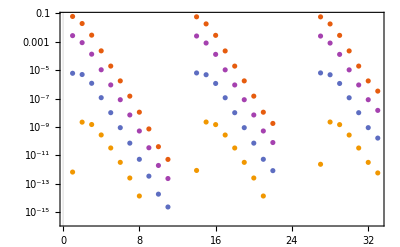

```mathematica
ListLogPlot[Abs[Transpose[photoDisTestResRepointed]],PlotRange->Full]
```

### Section 4.4 Kinetic decoupling

```mathematica
meanmassovere1[α1_,e1_,large_,T_]:=2 Sum[f[α1 j^6 hubbleT[e1]/hubbleT[e1 j^2],e1 j^2,T] j^2,{j,1.,large}]
```

```mathematica
kdEqnLHS[α1_,e1_,T_]:=2Sum[j^2/(Exp[e1 j^2/T]-1),{j,1,Ceiling[√(10.^3/α1)]}]
```

```mathematica
kdEqnRHS[α1_,e1_,T_]:=meanmassovere1[α1,e1,Ceiling[√(10.^3/α1)],T]((e1^3 hubbleT[T])/(α1 T^3 hubbleT[e1])-1)
```

Calculate the x_1 for kinetic decoupling

```mathematica
(*kdtab=Table[{10.^lα1,10.^le1,FindRoot[kdEqnLHS[10.^lα1,10.^le1 ev,T ev]== kdEqnRHS[10.^lα1,10.^le1 ev,T ev],{T,10.^(le1-lα1)}][[1,2]]},{lα1,-4.,-2.,0.5},{le1,Log10[2.],Log10[2.]+4,0.5}];*)
```

```mathematica
kdtab=dmwelData["T_kd"];kdtab2=Log10[Flatten[kdtab,1]];kdtab3={};For[i=1,i≤Length[kdtab2],i++,If[kdtab2[[i,2]]≥Log10[20000.]+kdtab2[[i,1]],AppendTo[kdtab3,kdtab2[[i]]]]];
```

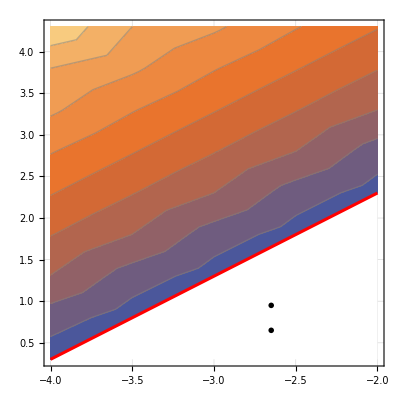

```mathematica
kdPlot=ListContourPlot[kdtab3,PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX["\\log_{10}(T_\\text{kd}/\\si{eV})",Magnification->1.3],LegendMarkerSize->300.,LabelStyle->13],BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,FrameLabel->{MaTeX["\\log_{10}\\alpha_1",Magnification->1.25],MaTeX["\\log_{10}E_1",Magnification->1.25]},GridLines->Automatic,PlotRange->{{-4.,-2.},{Log10[2.],Log10[2.]+4.}},ContourStyle->Gray];cmbPlot=Plot[Log10[20 10^(lα1+3)],{lα1,-4.0,-2.},GridLines->None,PlotStyle->{Thickness[.0055],Red},Filling->Bottom,FillingStyle->White];Tkdfig=Show[kdPlot,cmbPlot,Epilog->{Inset[MaTeX["\\color{red}\\text{Excluded by}",Magnification->1.5],{-2.65,0.95}],Inset[MaTeX["\\color{red}\\text{CMB anisotropies}",Magnification->1.5],{-2.65,0.65}]}]
```

```mathematica
Export["fig_Tkd.pdf",Tkdfig]
```

fig_Tkd.pdf

```mathematica
cutOffMass[k_]:=(4 π)/3(π/k)^3(ρdm0/.h->h18)/c^2/sm
```

Acoustic oscillation

```mathematica
kaoCalc[lα1_,le1_]:=π(gstarS[kdTab[[Round[2lα1+9],Round[2(le1-Log10[2.])+1],3]]]/gstarS0)^(1./3.) tcmbinev/(kdTab[[Round[2lα1+9],Round[2(le1-Log10[2.])+1],3]]ev)hubbleT[kdTab[[Round[2lα1+9],Round[2(le1-Log10[2.])+1],3]]ev]/c
```

```mathematica
(*cutOffMassaoTab=Flatten[Table[{10.^lα1,10.^le1,cutOffMass[kaoCalc[lα1,le1]]},{lα1,-4.,-2.,0.5},{le1,Log10[2.],Log10[2.]+4,0.5}],1];*)
```

```mathematica
cutOffMassaoTab=dmwelData["Cut-off mass: acoustic oscillation"];
```

Free-streaming

```mathematica
kfsCalc[mass_,Tkd_]:=(mass/Tkd)^(1/2)((gstarS[Tkd/ev]/gstarS0)^(1./3.)(Tkd/Teq18))/Log[4(gstarS[Tkd/ev]/gstarS0)^(1./3.)Tkd/ Teq18] keq18
```

```mathematica
(*cutOffMassfsTab=Flatten[Table[{10.^lα1,10.^le1,cutOffMass[kfsCalc[meanmassfo[10.^lα1,10.^le1 ev,Ceiling[√(10.^(3-lα1))]],kdTab[[Round[2lα1+9],Round[2(le1-Log10[2.])+1],3]]ev]]},{lα1,-4.,-2.,0.5},{le1,Log10[2.],Log10[2.]+4,0.5}],1];*)
```

```mathematica
cutOffMassfsTab=dmwelData["Cut-off mass: free-streaming"];
```

Damping

```mathematica
trelaxoverm[α1_,e1_,T_]:=(2 e1^2)/(α1 T^3 hubbleT[e1 ev]ev)(meanmassovere1[α1,e1 ev,Ceiling[√(10.^3/α1)],T ev]+kdEqnLHS[α1,e1,T])^-1
```

```mathematica
kdCalc[α1_,e1_,Tkd_]:=Re[((3 c^2 ev^3)/(2 tcmbinev^2 gstarS0^2)NIntegrate[trelaxoverm[α1,e1,Exp[lT]](gstarSdenom[Exp[lT] ev]Exp[3lT] gstarS[Exp[lT]]^2)/hubbleT[Exp[lT]ev],{lT,Log[Tkd],Log[10.^8]},PrecisionGoal->3, MaxPoints -> 20])^(-1/2)]
```

```mathematica
(*cutOffMassdTab=Flatten[Table[{10.^lα1,10.^le1,cutOffMass[kdCalc[10.^lα1,10.^le1,kdTab[[Round[2lα1+9],Round[2(le1-Log10[2.])+1],3]]]]},{lα1,-4.,-2.,0.5},{le1,Log10[2.],Log10[2.]+4,0.5}],1];*)
```

```mathematica
cutOffMassdTab=dmwelData["Cut-off mass: damping"];
```

Compare masses from free-streaming, damping and acoustic oscillations:

```mathematica
comp[list_]:={"FS","D","AO"}[[Ordering[list,-1][[1]]]];comparekTab=Join[{{"α_1","E_1","","M_fs","M_d","M_ao","",""}},Table[If[cutOffMassfsTab[[i,2]]≥20000.cutOffMassfsTab[[i,1]],{cutOffMassfsTab[[i,1]],cutOffMassfsTab[[i,2]],"",fsval=cutOffMassfsTab[[i,3]],dval=Re[cutOffMassdTab[[i,3]]],aoval=cutOffMassaoTab[[i,3]],"",comp[{fsval,dval,aoval}]},Null],{i,Length[cutOffMassfsTab]}]];pSF[comparekTab//TableForm,2]
```

α_1 | E_1 |  | M_fs | M_d | M_ao |  | 
 1.0×10^-4 |  2.0×10^0 |  |  4.5×10^3 |  1.3×10^1 |  4.5×10^4 |  | AO
 1.0×10^-4 |  6.3×10^0 |  |  1.2×10^2 |  4.0×10^-1 |  1.0×10^3 |  | AO
 1.0×10^-4 |  2.0×10^1 |  |  6.3×10^-1 |  7.8×10^-3 |  4.7×10^-1 |  | FS
 1.0×10^-4 |  6.3×10^1 |  |  8.5×10^-3 |  8.6×10^-5 |  1.0×10^-2 |  | AO
 1.0×10^-4 |  2.0×10^2 |  |  1.8×10^-4 |  1.6×10^-6 |  3.0×10^-4 |  | AO
 1.0×10^-4 |  6.3×10^2 |  |  5.5×10^-6 |  4.6×10^-8 |  9.4×10^-6 |  | AO
 1.0×10^-4 |  2.0×10^3 |  |  1.3×10^-7 |  1.6×10^-9 |  1.1×10^-7 |  | FS
 1.0×10^-4 |  6.3×10^3 |  |  4.6×10^-9 |  3.9×10^-24 |  3.1×10^-9 |  | FS
 1.0×10^-4 |  2.0×10^4 |  |  1.1×10^-11 |  0.0×10^0 |  1.5×10^-13 |  | FS
Null |  |  |  |  |  |  | 
 3.2×10^-4 |  6.3×10^0 |  |  7.3×10^3 |  2.1×10^1 |  3.3×10^4 |  | AO
 3.2×10^-4 |  2.0×10^1 |  |  2.5×10^2 |  8.6×10^-1 |  9.1×10^2 |  | AO
 3.2×10^-4 |  6.3×10^1 |  |  1.4×10^0 |  1.7×10^-2 |  4.3×10^-1 |  | FS
 3.2×10^-4 |  2.0×10^2 |  |  2.0×10^-2 |  2.0×10^-4 |  1.0×10^-2 |  | FS
 3.2×10^-4 |  6.3×10^2 |  |  4.3×10^-4 |  3.7×10^-6 |  3.0×10^-4 |  | FS
 3.2×10^-4 |  2.0×10^3 |  |  1.3×10^-5 |  1.1×10^-7 |  9.4×10^-6 |  | FS
 3.2×10^-4 |  6.3×10^3 |  |  3.1×10^-7 |  3.9×10^-9 |  1.1×10^-7 |  | FS
 3.2×10^-4 |  2.0×10^4 |  |  1.1×10^-8 |  1.1×10^-22 |  3.1×10^-9 |  | FS
Null |  |  |  |  |  |  | 
Null |  |  |  |  |  |  | 
 1.0×10^-3 |  2.0×10^1 |  |  1.5×10^4 |  4.2×10^1 |  2.9×10^4 |  | AO
 1.0×10^-3 |  6.3×10^1 |  |  5.6×10^2 |  1.8×10^0 |  8.7×10^2 |  | AO
 1.0×10^-3 |  2.0×10^2 |  |  3.2×10^0 |  3.9×10^-2 |  4.1×10^-1 |  | FS
 1.0×10^-3 |  6.3×10^2 |  |  4.7×10^-2 |  4.7×10^-4 |  1.0×10^-2 |  | FS
 1.0×10^-3 |  2.0×10^3 |  |  1.0×10^-3 |  8.8×10^-6 |  3.0×10^-4 |  | FS
 1.0×10^-3 |  6.3×10^3 |  |  3.1×10^-5 |  2.6×10^-7 |  9.4×10^-6 |  | FS
 1.0×10^-3 |  2.0×10^4 |  |  7.2×10^-7 |  9.2×10^-9 |  1.1×10^-7 |  | FS
Null |  |  |  |  |  |  | 
Null |  |  |  |  |  |  | 
Null |  |  |  |  |  |  | 
 3.2×10^-3 |  6.3×10^1 |  |  3.4×10^4 |  9.5×10^1 |  2.8×10^4 |  | FS
 3.2×10^-3 |  2.0×10^2 |  |  1.3×10^3 |  4.2×10^0 |  8.6×10^2 |  | FS
 3.2×10^-3 |  6.3×10^2 |  |  7.5×10^0 |  9.2×10^-2 |  4.1×10^-1 |  | FS
 3.2×10^-3 |  2.0×10^3 |  |  1.1×10^-1 |  1.1×10^-3 |  1.0×10^-2 |  | FS
 3.2×10^-3 |  6.3×10^3 |  |  2.4×10^-3 |  2.1×10^-5 |  3.0×10^-4 |  | FS
 3.2×10^-3 |  2.0×10^4 |  |  7.3×10^-5 |  6.1×10^-7 |  9.4×10^-6 |  | FS
Null |  |  |  |  |  |  | 
Null |  |  |  |  |  |  | 
Null |  |  |  |  |  |  | 
Null |  |  |  |  |  |  | 
 1.0×10^-2 |  2.0×10^2 |  |  7.9×10^4 |  2.2×10^2 |  2.7×10^4 |  | FS
 1.0×10^-2 |  6.3×10^2 |  |  3.1×10^3 |  9.8×10^0 |  8.5×10^2 |  | FS
 1.0×10^-2 |  2.0×10^3 |  |  1.8×10^1 |  2.2×10^-1 |  4.0×10^-1 |  | FS
 1.0×10^-2 |  6.3×10^3 |  |  2.6×10^-1 |  2.6×10^-3 |  1.0×10^-2 |  | FS
 1.0×10^-2 |  2.0×10^4 |  |  5.8×10^-3 |  5.0×10^-5 |  3.0×10^-4 |  | FS

Plot cut-off mass

```mathematica
coMfsTab=Log10[Table[{{cutOffMassfsTab[[i,1]],cutOffMassfsTab[[i,2]]},cutOffMassfsTab[[i,3]]},{i,Length[cutOffMassfsTab]}]];cMfsFn=Interpolation[coMfsTab];coMaoTab=Log10[Table[{{cutOffMassaoTab[[i,1]],cutOffMassaoTab[[i,2]]},cutOffMassaoTab[[i,3]]},{i,Length[cutOffMassaoTab]}]];cMaoFn=Interpolation[coMaoTab];
```

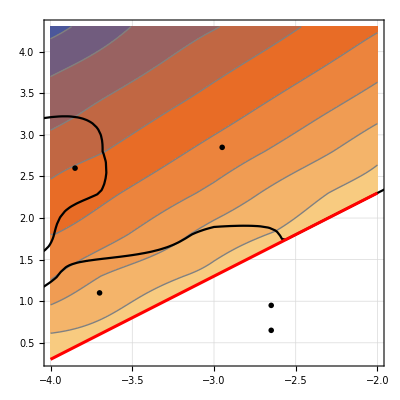

```mathematica
cp=ContourPlot[If[le1≥Log10[20000.]+lα1,Max[cMfsFn[lα1,le1],cMaoFn[lα1,le1]],Null],{lα1,-4.,-2.},{le1,Log10[2.],Log10[2.]+4.},PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX["M_\\text{cut}/M_\\Sun",Magnification->1.3],LegendMarkerSize->300.,LabelStyle->13],BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,FrameLabel->{MaTeX["\\log_{10}\\alpha_1",Magnification->1.25],MaTeX["\\log_{10}E_1",Magnification->1.25]},GridLines->Automatic,PlotRange->{{-4.,-2.},{Log10[2.],Log10[2.]+4.}},PlotPoints->100,ContourStyle->Gray];rp=RegionPlot[(cMfsFn[lα1,le1]>cMaoFn[lα1,le1])&&(le1≥Log10[20000.]+lα1),{lα1,-4.05,-1.95},{le1,Log10[2.],Log10[2.]+5.},GridLines->{Automatic,Range[0,4.5,0.5]},PlotStyle->None,BoundaryStyle->{Thick,Black},PlotRange->{{-4.,-2.},{Log10[2.],Log10[2.]+4.}},PlotRangeClipping->True];
pp=ParametricPlot[{lα1,Log10[20 10^(lα1+3)]},{lα1,-4.0,-2.},GridLines->None,PlotStyle->{Thickness[.0055],Red}];figCutOff=Show[cp,rp,pp,Epilog->{Inset[MaTeX["\\text{Free-streaming}",Magnification->1.5],{-2.95,2.85}],
Inset[MaTeX["\\text{AO}",Magnification->1.5],{-3.85,2.6}],Inset[MaTeX["\\text{AO}",Magnification->1.5],{-3.7,1.1}],Inset[MaTeX["\\color{red}\\text{Excluded by}",Magnification->1.5],{-2.65,0.95}],Inset[MaTeX["\\color{red}\\text{CMB anisotropies}",Magnification->1.5],{-2.65,0.65}]}]
```

```mathematica
Export["fig_cut_off.pdf",figCutOff]
```

fig_cut_off.pdf

The cut-off mass associated with Lyman-α constraints

```mathematica
pSF[cutOffMass[Quantity[h18,("Megaparsecs")^-1]],1]
```

1.×10^13

## Section 5 Laboratory detection

Calculate the overdensity of dark matter local to present-day Earth

```mathematica
δdm=Quantity[0.5,("Gigaelectronvolts")/("Centimeters")^3]/ρdm0
```

395319.

European XFEL

From Tschentscher+ table 3

```mathematica
XFELen={243,790,1680,6200,13300,30800} ev;
```

```mathematica
XFELavInt={5.9 10^18,1.8 10^18,9.3 10^17,6.2 10^16,2.1 10^16,1.3 10^15}Quantity[("Seconds")^-1];
```

```mathematica
XFELTotEnRate=XFELen XFELavInt
```

{1.4337×10^21 eV/s,1.422×10^21 eV/s,1.5624×10^21 eV/s,3.844×10^20 eV/s,2.793×10^20 eV/s,4.004×10^19 eV/s}

So the maximum photon power is at 1680eV, giving

```mathematica
XFELpower=XFELTotEnRate[[3]]
```

1.5624×10^21 eV/s

```mathematica
XFELbeamwidth=Quantity[200. 10^-4,"Centimeters"]
```

0.02 cm

Say 10fs pulse at this power (from 2-100fs range quoted in Tsh... and Feidenhaus pp21-28 Synchrotron Radiation New Vol 30 2017 Issue 6)

```mathematica
ndm0ref=ρdm0/massfoTab[[3,3,3]]
```

0.0000688279 /cm^3

```mathematica
XFELnumberEmissionCoeff=UnitConvert[2 ndm0ref δdm  Abar1coeff/(√gstarE0) 0.5,1/("Electronvolts""Seconds")]
```

3.28194×10^-31 per secondper electronvolt

```mathematica
detectorLength=Quantity[1.,"Meters"];XFELemissionRate=UnitConvert[XFELnumberEmissionCoeff XFELpower detectorLength/c,("Years")^-1];pSF[XFELemissionRate,1]
```

5.×10^-11 per year

```mathematica
powerIncreaseFactor=Quantity[10.,("Years")^-1]/XFELemissionRate;pSF[powerIncreaseFactor,1]
```

2.×10^11

```mathematica
NSum[j^-2,{j,1000}]
```

1.64393

## Appendices

### A Validity of the governing equation for excitation fractions

#### Condition (1): sufficiently non-relativistic

Mass ratios

The following calculates the α1 =10^-3 data for Appendix A’s first figure, and also gives a table showing the lower end of the one standard deviation range

```mathematica
meanmassSimp[α1_,large_,x1_]:=2 Sum[fSimp[α1 j^2,x1 j^2] j^2,{j,1.large}];sdmassSimp[α1_,large_,x1_]:=√(2 Sum[(fSimp[α1 j^2,x1 j^2]-fSimp[α1 j^2,x1 j^2]^2)j^4,{j,1.large}])
```

The following calculates the α1 =10^-4,10^-3,10^-2 data for Appendix A’s first figure, and also gives a table showing the lower end of the one standard deviation range

```mathematica
pointsM4=Join[Range[-8.,-6.],Range[-5.8,-4.2,0.2],Range[-4.,2.]];ratioTableM4=With[{α1=10.^-4},large=25 Ceiling[√(10.^3/α1)];Table[{10.^pointsM4[[i]],10.^pointsM4[[i]] meanmassSimp[α1,large,10.^pointsM4[[i]]],10.^pointsM4[[i]] sdmassSimp[α1,large,10.^pointsM4[[i]]]},{i,1,Length[pointsM4]}]];Table[{ratioTableM4[[i,1]],ratioTableM4[[i,2]]-ratioTableM4[[i,3]]},{i,1,Length[ratioTableM4]}]//TableForm
```

1.×10^-8 | 6680.09
1.×10^-7 | 2087.68
1.×10^-6 | 671.186
1.58489×10^-6 | 542.925
2.51189×10^-6 | 445.516
3.98107×10^-6 | 374.963
6.30957×10^-6 | 329.309
0.00001 | 309.421
0.0000158489 | 320.238
0.0000251189 | 372.532
0.0000398107 | 485.142
0.0000630957 | 688.665
0.0001 | 1031.89
0.001 | 9844.73
0.01 | 98392.2
0.1 | 983919.
1. | 9.83919×10^6
10. | 9.83919×10^7
100. | 9.83919×10^8

```mathematica
pointsM3=Join[Range[-8.,-5.],Range[-4.8,-3.2,0.2],Range[-3.,2.]];ratioTableM3=With[{α1=0.001},large=25 Ceiling[√(10.^3/α1)];Table[{10.^pointsM3[[i]],10.^pointsM3[[i]] meanmassSimp[α1,large,10.^pointsM3[[i]]],10.^pointsM3[[i]] sdmassSimp[α1,large,10.^pointsM3[[i]]]},{i,1,Length[pointsM3]}]];Table[{ratioTableM3[[i,1]],ratioTableM3[[i,2]]-ratioTableM3[[i,3]]},{i,1,Length[ratioTableM3]}]//TableForm
```

1.×10^-8 | 6630.17
1.×10^-7 | 2087.61
1.×10^-6 | 646.224
0.00001 | 204.011
0.0000158489 | 164.082
0.0000251189 | 133.689
0.0000398107 | 111.43
0.0000630957 | 96.4223
0.0001 | 88.4787
0.000158489 | 88.4995
0.000251189 | 98.9777
0.000398107 | 124.49
0.000630957 | 172.509
0.001 | 254.925
0.01 | 2401.33
0.1 | 23996.
1. | 239958.
10. | 2.39958×10^6
100. | 2.39958×10^7

```mathematica
pointsM2=Join[Range[-8.,-4.],Range[-3.8,-2.2,0.2],Range[-2.,2.]];ratioTableM2=With[{α1=0.01},large=100 Ceiling[√(10.^3/α1)];Table[{10.^pointsM2[[i]],10.^pointsM2[[i]] meanmassSimp[α1,large,10.^pointsM2[[i]]],10.^pointsM2[[i]] sdmassSimp[α1,large,10.^pointsM2[[i]]]},{i,1,Length[pointsM2]}]];Table[{ratioTableM2[[i,1]],ratioTableM2[[i,2]]-ratioTableM2[[i,3]]},{i,1,Length[ratioTableM2]}]//TableForm
```

1.×10^-8 | 6678.73
1.×10^-7 | 2087.61
1.×10^-6 | 646.201
0.00001 | 196.505
0.0001 | 59.8819
0.000158489 | 47.6105
0.000251189 | 38.2299
0.000398107 | 31.2204
0.000630957 | 26.1532
0.001 | 22.7109
0.00158489 | 20.8056
0.00251189 | 20.7118
0.00398107 | 23.101
0.00630957 | 29.0965
0.01 | 40.4696
0.1 | 359.059
1. | 3585.12
10. | 35850.9
100. | 358509.

```mathematica
nonrel=Show[ListLogLogPlot[{Table[{ratioTableM2[[n,1]],ratioTableM2[[n,2]]},{n,1,Length[ratioTableM2]}],Table[{ratioTableM2[[n,1]],ratioTableM2[[n,2]]-ratioTableM2[[n,3]]},{n,1,Length[ratioTableM2]}],Table[{ratioTableM2[[n,1]],ratioTableM2[[n,2]]+ratioTableM2[[n,3]]},{n,1,Length[ratioTableM2]}]},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,PlotRange->{Full,{1,10^8}},Filling->{1->{2},1->{3}},FillingStyle->Thick,PlotMarkers->{"●","",""},PlotStyle->RGBColor[0.945109, 0.593901, 0.],FrameLabel->{MaTeX["x_1",Magnification->1.25],MaTeX["r",Magnification->1.25]},GridLines->Automatic],ListLogLogPlot[{Table[{ratioTableM3[[n,1]],ratioTableM3[[n,2]]},{n,1,Length[ratioTableM3]}],Table[{ratioTableM3[[n,1]],ratioTableM3[[n,2]]-ratioTableM3[[n,3]]},{n,1,Length[ratioTableM3]}],Table[{ratioTableM3[[n,1]],ratioTableM3[[n,2]]+ratioTableM3[[n,3]]},{n,1,Length[ratioTableM3]}]},PlotRange->{Full,{1,10^8}},Filling->{1->{2},1->{3}},FillingStyle->Thick,PlotMarkers->{"■","",""},PlotStyle->RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023]],ListLogLogPlot[{Table[{ratioTableM4[[n,1]],ratioTableM4[[n,2]]},{n,1,Length[ratioTableM4]}],Table[{ratioTableM4[[n,1]],ratioTableM4[[n,2]]-ratioTableM4[[n,3]]},{n,1,Length[ratioTableM4]}],Table[{ratioTableM4[[n,1]],ratioTableM4[[n,2]]+ratioTableM4[[n,3]]},{n,1,Length[ratioTableM4]}]},PlotRange->{Full,{1,10^8}},Filling->{1->{2},1->{3}},FillingStyle->Thick,PlotMarkers->{"▲","",""},PlotStyle->RGBColor[0.365248, 0.427802, 0.758297]],Epilog->{{EdgeForm[Black],White,Rectangle[{Log[10^-6.7],Log[10^4.4]},{Log[10^-4.7],Log[10^7.8]}]},Inset[Grid[{{MaTeX["\\alpha_1",Magnification->1.25],SpanFromLeft},{Style["●",RGBColor[0.945109, 0.593901, 0.]],"10^-2"},{Style["■",RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023]],"10^-3"},{Style["▲",RGBColor[0.365248, 0.427802, 0.758297]],"10^-4"}}],Scaled[{0.275,0.775}]]}]
```

-Graphics-

```mathematica
Export["fig_non_rel.pdf",nonrel]
```

fig_non_rel.pdf

Relativistic coefficients for the governing equation

```mathematica
mj[massRatio_,γ_]:=(massRatio γ^2 √(1-1/γ^2))/BesselK[2,massRatio] Exp[-massRatio γ];
Tratio[v_,θ_]:=(√(1-v^2))/(1-v Cos[θ]);
coeffConstant[x_]:=1/(Exp[x]-1);
coeffMinusf[x_]:=(Exp[x]+1)/(Exp[x]-1);
coeffConstantLorentz[β_,θ_,x_]:=Tratio[β,θ]^4/(Exp[x/Tratio[β,θ]]-1);
coeffMinusfLorentz[β_,θ_,x_]:=(Tratio[β,θ]^4(Exp[x/Tratio[β,θ]]+1))/(Exp[x/Tratio[β,θ]]-1);
```

```mathematica
With[{massRatio1=20.,massRatio2=90.,massRatio3=300.,x=1.},NumberForm[{NIntegrate[1/2 Sin[θ]mj[massRatio1,γ]coeffConstantLorentz[√(1-1/γ^2),θ,x],{θ,0,π},{γ,1,∞}]/coeffConstant[x],NIntegrate[1/2 Sin[θ]mj[massRatio2,γ]coeffConstantLorentz[√(1-1/γ^2),θ,x],{θ,0,π},{γ,1,∞}]/coeffConstant[x],NIntegrate[1/2 Sin[θ]mj[massRatio3,γ]coeffConstantLorentz[√(1-1/γ^2),θ,x],{θ,0,π},{γ,1,∞}]/coeffConstant[x]},3]]
```

{1.61,1.11,1.03}

```mathematica
With[{massRatio1=20.,massRatio2=90.,massRatio3=300.,x=10.},NumberForm[{NIntegrate[1/2 Sin[θ]mj[massRatio1,γ]coeffMinusfLorentz[√(1-1/γ^2),θ,x],{θ,0,π},{γ,1,∞}]/coeffMinusf[x],NIntegrate[1/2 Sin[θ]mj[massRatio2,γ]coeffMinusfLorentz[√(1-1/γ^2),θ,x],{θ,0,π},{γ,1,∞}]/coeffMinusf[x],NIntegrate[1/2 Sin[θ]mj[massRatio3,γ]coeffMinusfLorentz[√(1-1/γ^2),θ,x],{θ,0,π},{γ,1,∞}]/coeffMinusf[x]},4]]
```

{1.227,1.046,1.013}

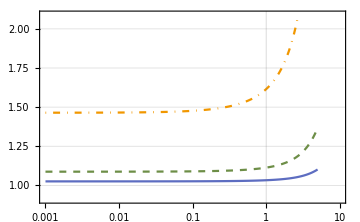

```mathematica
figfindep=With[{massRatio1=20.,massRatio2=90.,massRatio3=300.},LogLinearPlot[{NIntegrate[1/2 Sin[θ]mj[massRatio3,γ]coeffConstantLorentz[√(1-1/γ^2),θ,x],{θ,0,π},{γ,1,∞}]/coeffConstant[x],NIntegrate[1/2 Sin[θ]mj[massRatio2,γ]coeffConstantLorentz[√(1-1/γ^2),θ,x],{θ,0,π},{γ,1,∞}]/coeffConstant[x],NIntegrate[1/2 Sin[θ]mj[massRatio1,γ]coeffConstantLorentz[√(1-1/γ^2),θ,x],{θ,0,π},{γ,1,∞}]/coeffConstant[x]},{x,10.^-3,5.},ImageSize->Medium,PlotStyle->relstyles,GridLines->{{1.},Automatic},FrameLabel->MaTeX["x",Magnification->1.25],PlotRange->{{10.^-3,10.},{0.91,2.09}},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,FrameTicks->{{Automatic,None},{Automatic,Automatic}}]]
```

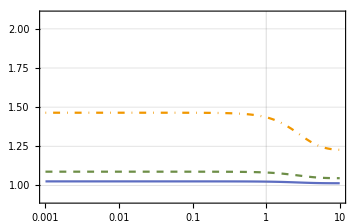

```mathematica
figfcoefficient=With[{massRatio1=20.,massRatio2=90.,massRatio3=300.},Show[LogLinearPlot[{NIntegrate[1/2 Sin[θ]mj[massRatio3,γ]coeffMinusfLorentz[√(1-1/γ^2),θ,x],{θ,0,π},{γ,1,∞}]/coeffMinusf[x],NIntegrate[1/2 Sin[θ]mj[massRatio2,γ]coeffMinusfLorentz[√(1-1/γ^2),θ,x],{θ,0,π},{γ,1,∞}]/coeffMinusf[x],NIntegrate[1/2 Sin[θ]mj[massRatio1,γ]coeffMinusfLorentz[√(1-1/γ^2),θ,x],{θ,0,π},{γ,1,∞}]/coeffMinusf[x]},{x,10.^-3,10.},PlotLegends->{MaTeX["r=300",Magnification->1.25],MaTeX["r=90",Magnification->1.25],MaTeX["r=20",Magnification->1.25]},ImageSize->Medium,PlotStyle->relstyles,GridLines->{{1.},Automatic},FrameLabel->MaTeX["x"],PlotRange->{{10.^-3,10.},{0.91,2.09}},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,FrameTicks->{{Automatic,None},{Automatic,Automatic}}]]]
```

```mathematica
figrel=Grid[{{figfindep,figfcoefficient}},Spacings->{3,Automatic}]
```

-Graphics- | -Graphics-

```mathematica
Export["fig_rel.pdf",figrel]
```

fig_rel.pdf

```mathematica
meanmassSimpRel[α1_,large_,x1_]:=2 Sum[fSimp[α1 j^2,x1 j^2] j^2,{j,1.large}];
```

#### Condition (2): photon energy much less than DMWEL mass

Absorption/Stimulated Emission

The following sets eγ=en (1+varγratio) to calculate that varγratio

Absorption

```mathematica
FullSimplify[Solve[{m+en(1+varγratio)==(m+en)/(√(1-v^2)),en(1+varγratio)==((m+en) v)/(√(1-v^2))},{varγratio,v}]][[1,1]]
```

varγratio→en/(2 m)

Stimulated Emission (using that the stimulating and stimulated photons are identical due to coherence)

```mathematica
FullSimplify[Solve[{m+en+en(1+varγratio)==m/(√(1-v^2))+2en(1+varγratio),en(1+varγratio)==(m v)/(√(1-v^2))+2en(1+varγratio)},{varγratio,v}]][[1,1]]
```

varγratio→-en/(2 (en+m))

The following calculates the probability of an emission or absorption having energy a fraction, tolerance, or more of the mass.  It weights emissions/absorptions by their energy.  In the function, tolerance is multiplied by 2 to reflect the 2 in the varγratio=en/(2m)

```mathematica
probAbsStimEm[α1_,large_,x1_,tolerance_]:=Sum[1/(x1^3(ⅇ^(x1 j^2)-1)j^2),{j,√((meanmassSimp[α1,large,x1]-sdmassSimp[α1,large,x1])(2tolerance)),large}]/Sum[1/(x1^3(ⅇ^(x1 j^2)-1)j^2),{j,1,large}]
```

```mathematica
energyConditionTab=Table[{10.^logx1,probAbsStimEm[10.^lα1,10.^((3-lα1)/2),10.^logx1,0.01]},{lα1,-2.,-4.,-1.},{logx1,-6.,2.,0.25}];
```

```mathematica
energyConditionTab//TableForm
```

0.00001
0. | 0.0000177828
0. | 0.0000316228
2.74826×10^-9 | 0.0000562341
1.35384×10^-8 | 0.0001
7.11336×10^-8 | 0.000177828
3.46187×10^-7 | 0.000316228
1.52256×10^-6 | 0.000562341
6.02351×10^-6 | 0.001
0.0000211111 | 0.00177828
0.0000626041 | 0.00316228
0.000141624 | 0.00562341
0.000220527 | 0.01
0.000232393 | 0.0177828
0.000168958 | 0.0316228
0.0000791105 | 0.0562341
0.0000184089 | 0.1
1.20467×10^-6 | 0.177828
7.67932×10^-9 | 0.316228
7.09362×10^-13 | 0.562341
3.1679×10^-20 | 1.
1.72242×10^-33 | 1.77828
2.88953×10^-57 | 3.16228
1.0635×10^-99 | 5.62341
2.97805×10^-175 | 10.
1.23258×10^-309 | 17.7828
0. | 31.6228
0. | 56.2341
0. | 100.
0.
0.00001
2.32006×10^-11 | 0.0000177828
2.07712×10^-10 | 0.0000316228
1.35897×10^-9 | 0.0000562341
6.61497×10^-9 | 0.0001
2.31433×10^-8 | 0.000177828
5.24072×10^-8 | 0.000316228
6.5051×10^-8 | 0.000562341
3.64502×10^-8 | 0.001
6.75871×10^-9 | 0.00177828
2.18335×10^-10 | 0.00316228
3.63857×10^-13 | 0.00562341
3.45214×10^-18 | 0.01
3.53434×10^-27 | 0.0177828
3.19765×10^-43 | 0.0316228
7.68176×10^-72 | 0.0562341
6.97454×10^-123 | 0.1
7.72272×10^-214 | 0.177828
0. | 0.316228
0. | 0.562341
0. | 1.
0. | 1.77828
0. | 3.16228
0. | 5.62341
0. | 10.
0. | 17.7828
0. | 31.6228
0. | 56.2341
0. | 100.
0.
0.00001
1.61926×10^-12 | 0.0000177828
2.40697×10^-12 | 0.0000316228
6.69282×10^-13 | 0.0000562341
1.45517×10^-14 | 0.0001
5.266×10^-18 | 0.000177828
1.87634×10^-24 | 0.000316228
3.8948×10^-36 | 0.000562341
4.73023×10^-57 | 0.001
2.45363×10^-94 | 0.00177828
1.04979×10^-160 | 0.00316228
8.55031×10^-279 | 0.00562341
0. | 0.01
0. | 0.0177828
0. | 0.0316228
0. | 0.0562341
0. | 0.1
0. | 0.177828
0. | 0.316228
0. | 0.562341
0. | 1.
0. | 1.77828
0. | 3.16228
0. | 5.62341
0. | 10.
0. | 17.7828
0. | 31.6228
0. | 56.2341
0. | 100.
0.

```mathematica
figEnergyCondition=ListLogLogPlot[energyConditionTab,PlotStyle->{RGBColor[0.945109, 0.593901, 0.],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.365248, 0.427802, 0.758297]},PlotRange->{Automatic,{0.5 10.^-13,5 0.1}},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,FrameLabel->{MaTeX["x_1"],MaTeX["P_{x_1}"]},GridLines->Automatic,PlotMarkers->{"●","■","▲"},Epilog->{{EdgeForm[Black],White,Rectangle[{Log[10^-5.6],Log[10^-6.4]},{Log[10^-4.2],Log[10^-0.8]}]},Inset[Grid[{{MaTeX["\\alpha_1",Magnification->1.25],SpanFromLeft},{Style["●",RGBColor[0.945109, 0.593901, 0.]],"10^-2"},{Style["■",RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023]],"10^-3"},{Style["▲",RGBColor[0.365248, 0.427802, 0.758297]],"10^-4"}}],Scaled[{0.18,0.775}]]}]
```

-Graphics-

```mathematica
Export["fig_energy_cond.pdf",figEnergyCondition]
```

fig_energy_cond.pdf

#### Photons are thermal bath - and limit on number of levels

Find the number density n_● at the reference parameters (α_1,E_1)=(10^-3,20eV)

```mathematica
refn0=Quantity[10^ndm0TabLog[[21,3]],("Centimeters")^-3];pSF[refn0,1]
```

7.×10^-5 /cm^3

Solve analytically the modified equation for ρ_γ

```mathematica
ργmodres=DSolveValue[{D[ργmod[T],T]==(4ργmod[T])/T- n0overno0ref(e1overe1ref)^(-1/2)(2 ev^3 refn0 T^4)/tcmbinev^3 Quantity[("Centimeters")^3]/(2 √(T 20.)),ργmod[200 10.^9]==427/8 photonenergydensityboth[200 10.^9 ev]Quantity[("Centimeters")^3/("Electronvolts")]},ργmod,{T,200 10.^9,10.^20}];ScientificForm[Simplify[ργmodres[10.^9 TinGeV]/10.^45],1]
```

1/(√e1overe1ref)((5.×10^6) √e1overe1ref TinGeV^4.+(1.×10^3) n0overno0ref TinGeV^4.-(8.×10^1) n0overno0ref TinGeV^5.)

Find the temperature at which the modified ρ_γdiffers from its standard value by 1%

```mathematica
TinGeVOnePercent=Simplify[Solve[(ργmodres[10.^9 TinGeV])/(427/8 photonenergydensityboth[TinGeV gev]Quantity[("Centimeters")^3/("Electronvolts")])==0.99,TinGeV][[1,1,2]]]
```

3.7011×10^9 (0.000232461+(0.01 √e1overe1ref)/n0overno0ref)^2.

```mathematica
TinGeVOnePercentMain=3.701099536543492*^9 ((0.010000000000000222 √e1overe1ref)/n0overno0ref)^2;ScientificForm[TinGeVOnePercentMain,1]
```

((4.×10^5) e1overe1ref)/n0overno0ref^2

```mathematica
jOnePercent=Assuming[n0overno0ref>0,FullSimplify[√(TinGeVOnePercentMain/(20. 10^-9 e1overe1ref))]];ScientificForm[jOnePercent,1]
```

(4.×10^6)/n0overno0ref

Now find the asymptotic temperature.  It’s the non-zero solution below, and only the first term is non-negligible

```mathematica
TAsympinGeV=Solve[ργmodres[10.^9 TinGeV]==0,TinGeV][[2,1,2]];ScientificForm[TAsymp,1]
```

((4.×10^9) e1overe1ref+(2.×10^6) √e1overe1ref n0overno0ref+(2.×10^2) n0overno0ref^2)/n0overno0ref^2

Although not used in the paper, here’s a plot of  ργmodres at the reference parameters, showing the asymptotic

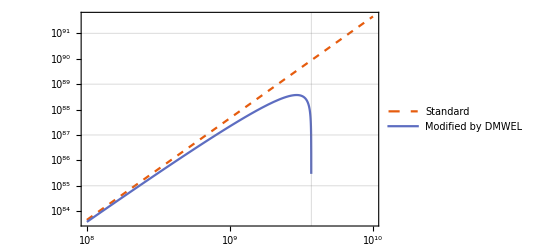

```mathematica
figasymp=LogLogPlot[{427/8 photonenergydensityboth[TinGeV gev]Quantity[("Centimeters")^3/("Electronvolts")],ργmodres[10.^9 TinGeV]/.{n0overno0ref->1,e1overe1ref->1}},{TinGeV,10.^8,10.^10},PlotLegends->{"Standard","Modified by DMWEL"},PlotStyle->{Dashed,Automatic},GridLines->{{TAsympinGeV/.{n0overno0ref->1,e1overe1ref->1}},Automatic},FrameLabel->{MaTeX["\\sfrac{T}{\\si{GeV}}",Magnification->1.5],MaTeX["\\sfrac{\\rho_\\gamma}{\\si{GeV}}",Magnification->1.5]},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False]
```

### B Photodissociation of nuclei

This appendix calculates the electromagnetic cascade functions, enArray, fγArray, and, for completeness,  feArray.  The calculation takes several days, so the results are stored in the dmwel_data.data file

Set the injection energy/eV (some of these are also set in section 4.3 above)

```mathematica
(*EXgrid={10.^6.,2. 10.^6.,3. 10.^6.,5. 10.^6.,10.^7.,3. 10.^7.,10.^8.,10.^8.75};lEXgrid=Length[EXgrid];Tgrid={0.1,1.,10.,100.,10^2.8,10^3.,10^3.2,10^3.4,10^3.6,10^3.8,10^4.};
lTgrid=Length[Tgrid];
Ebottom=1. 10^6;*)
```

Initialise calculation

```mathematica
(*fγarray=ConstantArray[Null,{lEXgrid,lTgrid}];
fearray=ConstantArray[Null,{lEXgrid,lTgrid}];
enarray=ConstantArray[Null,{lEXgrid,lTgrid}];fγarray[[1]]=Table[Kγγ[Ebottom,Ebottom,Tgrid[[Tindex]]]/Γγ[Ebottom,Tgrid[[Tindex]]]^2,{Tindex,1,lTgrid}];fearray[[1]]=Table[Keγ[Ebottom,Ebottom,Tgrid[[Tindex]]]/(Γγ[Ebottom,Tgrid[[Tindex]]] Γe[Ebottom,Tgrid[[Tindex]]]),{Tindex,1,lTgrid}];
enarray[[1]]=ConstantArray[Ebottom,lTgrid];*)
```

Calculation

```mathematica
(*For[EXindex=2,EXindex≤lEXgrid,EXindex++,
EX=EXgrid[[EXindex]];
For[Tindex=1,Tindex≤lTgrid,Tindex++,
T=Tgrid[[Tindex]];
fineGrid=125;coarseGrid=175;nGrid=coarseGrid+fineGrid;fineGridPoint=Ebottom(EX/Ebottom)^0.8;coarseRatio=fineGridPoint/Ebottom;fineRatio=EX/fineGridPoint;lnWidthCoarse=Log[coarseRatio]/coarseGrid;lnWidthFine=Log[fineRatio]/fineGrid;fineGridFoot=nGrid+1-fineGrid;enGrid=Join[Table[N[Ebottom coarseRatio^(ii/(nGrid-fineGrid))],{ii,0,nGrid-fineGrid-1}],Table[N[fineGridPoint fineRatio^(ii/fineGrid)],{ii,0,fineGrid}]];
fγ=ConstantArray["γs",nGrid+1];fe=ConstantArray["es",nGrid+1];
sd=ConstantArray["sd",nGrid+1];If[(EX T)/masselectron^2<0.05,jmark=nGrid+1;sd[[jmark]]=Keγ[EX,EX,T]/ΓγEX EX,jmark="Method1"];
ΓγEX=Γγ[EX,T];fγ[[nGrid+1]]=Kγγ[EX,EX,T]/ΓγEX^2;fe[[nGrid+1]]=Keγ[EX,EX,T]/(ΓγEX Γe[EX,T]);
For[step=nGrid,step≥1,step--,
stage="start";
enStep=enGrid[[step]];
stage="fγ";fγ[[step]]=(Γγ[enStep,T]-opensimpsonfactor[nGrid+1,step]Kγγ[enStep,enStep,T] enStep)^-1(Kγγ[enStep,EX,T]/ΓγEX+opensimpsonWrapper[Table[Kγγ[enStep,enGrid[[j]],T] fγ[[j]] enGrid[[j]],{j,step+1,nGrid+1}],nGrid+1,step]+opensimpsonWrapper[Table[Kγe[enStep,enGrid[[j]],T] fe[[j]] enGrid[[j]],{j,step+1,nGrid+1}],nGrid+1,step]);
stage="jmarking2";
If[jmark≠"Method1",sd[[step]]=sdFn[step,T] enStep];
stage="fe";
fe[[step]]=If[jmark=="Method1",Γe[enStep,T]^-1(Keγ[enStep,EX,T]/ΓγEX+simpsonWrapper[Table[Keγ[enStep,enGrid[[j]],T] fγ[[j]] enGrid[[j]],{j,step,nGrid+1}],nGrid+1,step]+opensimpsonWrapper[Table[Kee[enStep,enGrid[[j]],T] fe[[j]] enGrid[[j]],{j,step+1,nGrid+1}],nGrid+1,step]),(enGrid[[jmark]]/enStep)^2 fe[[jmark]]+1/(aT[T] enStep^2)simpsonWrapper[Take[sd,{step,jmark}],jmark,step]];
stage="jmarking2";
If[(jmark=="Method1")&&((enStep T)/masselectron^2<0.05),jmark=step;sd[[jmark]]=Keγ[enStep,EX,T]/ΓγEX enStep];
If[ByteCount[{step,fγ,fe}]>=10^7,stage="Big file";Pause[11111111111111]]];
fγarray[[EXindex,Tindex]]=fγ;
fearray[[EXindex,Tindex]]=fe;
enarray[[EXindex,Tindex]]=enGrid;Export["tempres.m",{{EXindex,Tindex,step},fγarray,fearray,enarray}];]]*)
```

Check the results, once the fForestell function has been set up in section 4.3

Show that fForestell gives the same results as the original calculations

```mathematica
(*Manipulate[LogLogPlot[Evaluate[Table[10.^18 fForestell[EXgrid[[EXindex]],Tgrid[[Tindex]],10.^9 EnGeV],{Tindex,1,lTgrid}]],{EnGeV,10.^-9 Ebottom,10.^-9 EXgrid[[EXindex]]},ImageSize->Large,AspectRatio->6.8/6.2,PlotRange->{{10^-3,0.6},{10^10,10^45}},GridLines->Automatic,PlotStyle->fForestellColours,PlotLegends->LineLegend[fForestellColours,{"0.1eV","1eV","10eV","100eV","10^2.8eV","10^3eV","10^3.2eV","10^3.4eV","10^3.6eV","10^3.8eV","10^4eV"},LegendLabel->"Temperature"],PlotLabel->StringForm["E_X=`` eV",EXgrid[[EXindex]]]],{EXindex,2,lEXgrid,1}]*)
```

And check it varies sensibly with EX

```mathematica
(*Manipulate[LogLogPlot[Evaluate[Table[10.^18 fForestell[10^l10EX,Tgrid[[Tindex]],10.^9 EnGeV],{Tindex,1,lTgrid}]],{EnGeV,10.^-9 Ebottom,10.^-9 10^l10EX},ImageSize->Large,AspectRatio->6.8/6.2,PlotRange->{{10^-3,0.6},{10^10,10^45}},GridLines->Automatic,PlotStyle->fForestellColours,PlotLegends->LineLegend[fForestellColours,{"0.1eV","1eV","10eV","100eV","10^2.8eV","10^3eV","10^3.2eV","10^3.4eV","10^3.6eV","10^3.8eV","10^4eV"},LegendLabel->"Temperature"],PlotLabel->StringForm["E_X=`` eV",10^l10EX]],{l10EX,Log10[2 10.^6],Log10[10.^8.75],0.1}]*)
```

Do similarly with a joint grid of  EX and T

```mathematica
(*Manipulate[LogLogPlot[Evaluate[Table[10.^18 fForestell[10^logEX,10^logT,10.^9 EnGeV],{Tindex,1,lTgrid}]],{EnGeV,10.^-9 Ebottom,0.6},ImageSize->Large,AspectRatio->6.8/6.2,PlotRange->{{10^-3,0.6},{10^10,10^45}},GridLines->Automatic,PlotStyle->{Black,Thin},PlotLabel->StringForm["E_X=`` eV, T=`` eV",10^logEX,10^logT]],{logEX,6.1,8.75,.1},{logT,-1.,4.,.1}]*)
```

## Initialisation cells

#### Turn off error messages

As there are many irrelevant messages, for example number too small as a result of exponentials

```mathematica
$Messages={}
```

{}

#### Tools for manipulating small- or medium-sized data

Small- or medium- size implies downloading all the data is not too memory/time-consuming

```mathematica
dataFileExport[filename_,comments_,labels_,expns_]:=Block[{stream},stream=OpenWrite[filename];WriteString[stream,"(@@\n"];Write[stream,{{NotebookFileName[],Now[]},comments}];
WriteString[stream,"@@)\n\n(<<\n"];
Write[stream,labels];
WriteString[stream,">>)\n\n(::\n"];
Write[stream,expns];
WriteString[stream,"::)"];
Close[stream]]
```

```mathematica
dataAttributesImport[filename_]:=Module[{stream,res},Off[ToExpression::notstrbox];stream=OpenRead[filename];res=ToExpression[Read[stream,Record,RecordSeparators->{{"(@@"},{"@@)"}}]];Close[stream];Return[res]]
```

```mathematica
dataLabelsImport[filename_]:=Module[{stream,res},Off[ToExpression::notstrbox];stream=OpenRead[filename];res=ToExpression[Read[stream,Record,RecordSeparators->{{"(<<"},{">>)"}}]];Close[stream];Return[res]]
```

```mathematica
dataJustDataImport[filename_]:=Module[{stream,res},stream=OpenRead[filename];res=ToExpression[Read[stream,Record,RecordSeparators->{{"(::"},{"::)"}}]];Close[stream];Return[res]]
```

```mathematica
dataDataImport[filename_]:={dataLabelsImport[filename],dataJustDataImport[filename]}
```

```mathematica
dataSelect[data_,label_]:=data[[2,Position[data[[1]],label][[1,1]]]];
dmwelData[label_]:=dataSelect[dmwelDataImported,label]
```

#### Ensure data and notebook directories are the same, and import data

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
dmwelDataImported=dataDataImport["dmwel_data.data"];
```

#### Padded scientific form

Define a function to give scientific form numbers, with proper padding by zeros to the right of the decimal - with thanks to N.J. Evans at https://mathematica.stackexchange.com/questions/96832/scientific-form-with-padding-and-exponent :

```mathematica
pSF[x_,n_]:=PaddedForm[x,{n,n-1},ExponentFunction->(1 Quotient[#,1]&),NumberFormat->(Row@{#1,"×",Superscript["10",ToString[#3]]}&)]
```

#### Initialisation of constants (using values from PDG18)

To avoid Unit problems which sometimes occur

```mathematica
ClearSystemCache[];
```

The constants

Newton’s G

```mathematica
gn=Quantity[6.674 10^-11,("Meters")^3/("Kilograms"("Seconds")^2)]
```

6.674×10^-11 m^3/(kg s^2)

Speed of light

```mathematica
c=Quantity[299792458 10^2,("Centimeters")/("Seconds")]
```

29979245800 cm/s

Reduced Planck constant

```mathematica
hbar=Quantity[1.0545718 10^-34,"Joules""Seconds"]
```

1.05457×10^-34 s J

Boltzmann’s constant

```mathematica
kb=Quantity[1.38065 10^-23,"Joules"/"Kelvins"]
```

1.38065×10^-23 J/K

The Planck energy

```mathematica
ePl=UnitConvert[(√(gn/(hbar c^5)))^-1]
```

1.95613×10^9 kg m^2/s^2

The present day Omega for dark matter

```mathematica
Ωdm=0.12 h^-2
```

0.12/h^2

The present day critical density ρ_c, in keV cm^-3

```mathematica
ρc=Quantity[1.054 10^1 ,("Kiloelectronvolts")/("Centimeters")^3] h^2
```

h^2 (10.54 keV/cm^3)

The current cosmic dark matter energy density

```mathematica
ρdm0=Simplify[Ωdm ρc]
```

1.2648 keV/cm^3

CMB temperature at present day

```mathematica
tcmb=Quantity[2.7255,"Kelvins"]
```

2.7255 K

```mathematica
tcmbinev=UnitConvert[kb tcmb,"Electronvolts"];ScientificForm[tcmbinev]
```

2.34866×10^-4 eV

Helium mass fraction

```mathematica
yp=0.245;
```

Recombination

```mathematica
zrecomb=1090;temprecomb=zrecomb tcmbinev
```

0.256003 eV

Baryon number density

```mathematica
nb=Quantity[2.5 10^-7,("Centimeters")^-3]
```

2.5×10^-7 /cm^3

Hydrogen number density

```mathematica
nH=nb (1-yp)
```

1.8875×10^-7 /cm^3

One solar mass

```mathematica
sm=Quantity[1.99 10^30,"Kilograms"]
```

1.99×10^30 kg

Various electron volt quantities

```mathematica
ev=Quantity["Electronvolts"];
mev=Quantity["Megaelectronvolts"];gev=Quantity["Gigaelectronvolts"];refev=20 ev;
```

#### Hubble parameter data from the 2018 Planck paper (for consistency with the annihilation results) and degrees of freedom from Figure 1 of 1609.04979 On Effective Degrees of Freedom in the Early Universe - Husdal

Note degrees of freedom only work for temperatures less than or equal to 10 GeV  Have assumed a middle quark-hadron transition temperature of 160 MeV

```mathematica
h18=0.6766;hubble018=Quantity[100 h18,("Kilometers")/("Seconds" "Megaparsecs")];
keq18=Quantity[0.010339,("Megaparsecs")^-1];
zeq18=3387;
Teq18=zeq18 tcmbinev;
heq18=c keq18 (1+zeq18);
pann=Quantity[3.2 10^-28,("Centimeters")^3/("Seconds""Gigaelectronvolts")];
ΩΛ=0.6889;
gstarEgrid={{70000. ,gstarE0=3.36},{330000.,10.6},{17144880.,10.6},{100. 10.^6,18.00},{160. 10.^6,62.49},{2. 10.^9,82.50},{10. 10.^9,86.22},{125. 10.^9,385./4.},{173. 10.^9,427./4.}};
lngstarE=Interpolation[Log[gstarEgrid],InterpolationOrder->1];gstarE[T_]:=If[T<70000.,gstarE0,Exp[lngstarE[Log[T]]]];
hubbleT[T_]:=heq18 √(gstarE[T/ev]/(2gstarE0)(T/Teq18)^4+1/2(T/Teq18)^3+((ΩΛ hubble018^2)/heq18^2));hubble[z_]:=hubbleT[tcmbinev(1+z)];
gstarSgrid={{70000. ,gstarS0=3.91},{330000.,10.56},{17144880.,10.56},{100. 10.^6,17.55},{160. 10.^6,62.25},{2. 10.^9,81.80},{10. 10.^9,86.13},{125. 10.^9,385./4.},{gstarSmax=173. 10.^9,427./4.}};
lngstarS=Interpolation[Log[gstarSgrid],InterpolationOrder->1];gstarS[T_]:=If[T<70000.,gstarS0,Exp[lngstarE[Log[T]]]];
gstarSBlocks=Join[{1.},Table[1.+1/3.((Log[gstarSgrid[[i,2]]]-Log[gstarSgrid[[i-1,2]]])/(Log[gstarSgrid[[i,1]]]-Log[gstarSgrid[[i-1,1]]])),{i,2,Length[gstarSgrid]}],{1.}];changeHalfWidths=ConstantArray[1.4,Length[gstarSgrid]];changeHalfWidths[[4]]=1.05;gstarSTab=Flatten[Table[{{Log[gstarSgrid[[i,1]]]-Log[changeHalfWidths[[i]]],gstarSBlocks[[i]]},{Log[gstarSgrid[[i,1]]]+Log[changeHalfWidths[[i]]],gstarSBlocks[[i+1]]}},{i,Length[gstarSgrid]}],1];
gstarSpre=Interpolation[gstarSTab,InterpolationOrder->1];
gstarSdenom[T_]:=If[T<1.4gstarSmax ev,gstarSpre[Log[Max[50000.,T/ev]]],1];
dTdt[T_]:=(hubbleT[T]T)/gstarSdenom[T];
```

#### Figure-related

Set up the MaTeX package

```mathematica
Needs["MaTeX`"]
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xfrac}","\\usepackage[T1]{fontenc}","\\usepackage{siunitx}","\\usepackage{mathabx}","\\usepackage{xcolor}"}];
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};DefaultBaseStyle->texStyle;
```

For nice plots

```mathematica
$PlotTheme="Scientific";αcolours={RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.9, 0.36, 0.054]};αmarkers={{Graphics[{αcolours[[1]],Rectangle[{0,0}]}],0.025},{Graphics[{αcolours[[2]],Disk[{0,0}]}],0.025},{Graphics[{αcolours[[3]],Triangle[{{0,1/(√3)},{-1/2,-1/(2 √3)},{1/2,-1/(2 √3)}}]}],0.025},{Graphics[{αcolours[[4]],Rotate[Rectangle[{0,0}],π/4]}],0.025}};
relstyles={{RGBColor[0.365248, 0.427802, 0.758297]},{RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],Dashed},{RGBColor[0.945109, 0.593901, 0.],DotDashed}};
```

```mathematica
probticks={{10^-6,"\*SuperscriptBox[\(10\), \(-6\)]"},{10^-5,"\*SuperscriptBox[\(10\), \(-5\)]"},{10^-4,"\*SuperscriptBox[\(10\), \(-4\)]"},{10^-3,"\*SuperscriptBox[\(10\), \(-3\)]"},{10^-2,"\*SuperscriptBox[\(10\), \(-2\)]"},{10^-1,"\*SuperscriptBox[\(10\), \(-1\)]"},{1,"1"}};
```

```mathematica
fTicksY=Join[{{10^-6,"\*SuperscriptBox[\(10\), \(-6\)]",{0.01,0}},{10^-5,"\*SuperscriptBox[\(10\), \(-5\)]",{0.01,0}},{10^-4,"\*SuperscriptBox[\(10\), \(-4\)]",{0.01,0}},{10^-3,"\*SuperscriptBox[\(10\), \(-3\)]",{0.01,0}},{10^-2,"\*SuperscriptBox[\(10\), \(-2\)]",{0.01,0}},{10^-1,"\*SuperscriptBox[\(10\), \(-1\)]",{0.01,0}},{1,"1"}},Flatten[Table[{i 10.^n,"",{0.005,0}},{n,-7,0},{i,2,9}],1]];fTicksX=Join[{{10^-5,"\*SuperscriptBox[\(10\), \(-5\)]",{0.01,0}},{10^-4,"\*SuperscriptBox[\(10\), \(-4\)]",{0.01,0}},{10^-3,"\*SuperscriptBox[\(10\), \(-3\)]",{0.01,0}},{10^-2,"\*SuperscriptBox[\(10\), \(-2\)]",{0.01,0}},{10^-1,"\*SuperscriptBox[\(10\), \(-1\)]",{0.01,0}},{10^0,"\*SuperscriptBox[\(10\), \(0\)]",{0.01,0}},{10^1,"\*SuperscriptBox[\(10\), \(1\)]",{0.01,0}},{10^2,"\*SuperscriptBox[\(10\), \(2\)]",{0.01,0}},{10^3,"\*SuperscriptBox[\(10\), \(3\)]",{0.01,0}}},Flatten[Table[{i 10.^n,"",{0.005,0}},{n,-6,4},{i,2,9}],1]];
```

```mathematica
fomassTicksY=Join[{{10^4,"\*SuperscriptBox[\(10\), \(4\)]"},{10^5,"\*SuperscriptBox[\(10\), \(5\)]"},{10^6,"\*SuperscriptBox[\(10\), \(6\)]"},{10^7,"\*SuperscriptBox[\(10\), \(7\)]"},{10^8,"\*SuperscriptBox[\(10\), \(8\)]"}},Flatten[Table[{i 10.^n,"",{0.005,0}},{n,3,9},{i,2,9}],1]];
fomassTicksX=Join[{{10^-5,"\*SuperscriptBox[\(10\), \(-5\)]",{0.01,0}},{10^-4,"\*SuperscriptBox[\(10\), \(-4\)]",{0.01,0}},{10^-3,"\*SuperscriptBox[\(10\), \(-3\)]",{0.01,0}},{10^-2,"\*SuperscriptBox[\(10\), \(-2\)]",{0.01,0}}},Flatten[Table[{i 10.^n,"",{0.005,0}},{n,-5,-1},{i,2,9}],1]];
```

```mathematica
histoMagn=1.45;
histoEpilogs={MaTeX["\\alpha_1=10^{\\text{-}4}",Magnification->histoMagn],MaTeX["\\alpha_1=10^{\\text{-}3}",Magnification->histoMagn],MaTeX["\\alpha_1=10^{\\text{-}2}",Magnification->histoMagn],MaTeX["\\alpha_1=10^{\\text{-}1}",Magnification->histoMagn]};
histoTicks={
{{Table[{i,PaddedForm[i,{3,3}]},{i,0,0.015,0.005}],Table[{i,""},{i,0,0.015,0.005}]},{{0,{1 10^7,"1×\*SuperscriptBox[\(10\), \(7\)]"},{2 10^7,"2×\*SuperscriptBox[\(10\), \(7\)]"}},{{0,""},{1 10^7,""},{2 10^7,""}}}},
{{{{0,"0.000"},0.001,0.002,0.003},{{0,""},{0.001,""},{0.002,""},{0.003,""}}},{{0,{0.5 10^6,"0.5×\*SuperscriptBox[\(10\), \(6\)]"},{1. 10^6,"1.0×\*SuperscriptBox[\(10\), \(6\)]"}},{{0,""},{0.5 10^6,""},{1. 10^6,""}}}},
{{Table[{i,PaddedForm[i,{3,3}]},{i,0,0.006,0.002}],Table[{i,""},{i,0,0.006,0.002}]},{Range[0,60000,20000],Table[{i,""},{i,0,60000,20000}]}},
{{Table[{i,PaddedForm[i,{3,3}]},{i,0,0.040,0.010}],Table[{i,""},{i,0,0.040,0.010}]},{Range[0,2000,500],Table[{i,""},{i,0,2000,500}]}}
};
```

```mathematica
zl=300;zu=1200;
glAniso={None,{0,5,10,15}};imPad={{20,20},{Automatic,Automatic}};anisoMagn=1.45;anisoEpilogs={MaTeX["\\text{HIon }\\alpha_1=10^{\\text{-}4}",Magnification->histoMagn],MaTeX["\\alpha_1=10^{\\text{-}3}",Magnification->histoMagn],MaTeX["\\alpha_1=10^{\\text{-}2}",Magnification->histoMagn],MaTeX["\\alpha_1=10^{\\text{-}1}",Magnification->histoMagn]};anisotropyPlotRangeHIon={{265,1235},{-0.25,6.75}};anistropyFTSHIon={{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},{{Directive[FontOpacity->0],Automatic},{Directive[FontOpacity->0],Automatic}},{{Directive[FontOpacity->0],Automatic},{Directive[FontOpacity->0],Automatic}}};anistropyFTHIon={{{{{0,"0",{0.02,0}},{1,""},{2,""},{3,""},{4,""},{5,"5",{0.02,0}},{6,""},{7,""}},Automatic},{{{300,"",{0.02,0}},{400,""},{500,""},{600,"",{0.02,0}},{700,""},{800,""},{900,"",{0.02,0}},{1000,""},{1100,""},{1200,"",{0.02,0}}},Automatic}},{{{{0,"",{0.02,0}},{1,""},{2,""},{3,""},{4,""},{5,"",{0.02,0}},{6,""},{7,""}},Automatic},{{{300,"",{0.02,0}},{400,""},{500,""},{600,"",{0.02,0}},{700,""},{800,""},{900,"",{0.02,0}},{1000,""},{1100,""},{1200,"",{0.02,0}}},Automatic}},{{{{0,"",{0.02,0}},{1,""},{2,""},{3,""},{4,""},{5,"",{0.02,0}},{6,""},{7,""}},Automatic},{{{300,"",{0.02,0}},{400,""},{500,""},{600,"",{0.02,0}},{700,""},{800,""},{900,"",{0.02,0}},{1000,""},{1100,""},{1200,"",{0.02,0}}},Automatic}}};anisotropyPlotRangeHeat={{265,1235},{-0.25,18.75}};anistropyFTSHeat={{{Automatic,Automatic},{Automatic,Automatic}},{{Directive[FontOpacity->0],Automatic},{Automatic,Automatic}},{{Directive[FontOpacity->0],Automatic},{Automatic,Automatic}}};anistropyFTHeat={{Automatic,{{{300,"300",{0.025,0}},{400,""},{500,""},{600,"600",{0.025,0}},{700,""},{800,""},{900,"900",{0.025,0}},{1000,""},{1100,""},{1200,"1200",{0.025,0}}},Automatic}},{Automatic,{{{300,"300",{0.025,0}},{400,""},{500,""},{600,"600",{0.025,0}},{700,""},{800,""},{900,"900",{0.025,0}},{1000,""},{1100,""},{1200,"1200",{0.025,0}}},Automatic}},{Automatic,{{{300,"300",{0.025,0}},{400,""},{500,""},{600,"600",{0.025,0}},{700,""},{800,""},{900,"900",{0.025,0}},{1000,""},{1100,""},{1200,"1200",{0.025,0}}},Automatic}}};
```

```mathematica
emissionsSpectrum=Join[{{10^-15,"\*SuperscriptBox[\(10\), \(-15\)]",{0.01,0}},{10^-12,"\*SuperscriptBox[\(10\), \(-12\)]",{0.01,0}},
{10^-9,"\*SuperscriptBox[\(10\), \(-9\)]",{0.01,0}},
{10^-6,"\*SuperscriptBox[\(10\), \(-6\)]",{0.01,0}},{10^-3,"\*SuperscriptBox[\(10\), \(-3\)]",{0.01,0}},{10^0,"\*SuperscriptBox[\(10\), \(0\)]\ ",{0.01,0}},{10^3,"\*SuperscriptBox[\(10\), \(3\)]",{0.01,0}}},Table[{10.^n,"",{0.005,0}},{n,-20,4}],Table[{10.^n,"",{0.005,0}},{n,-21,5}]];
```

```mathematica
bbnticks={{50 10^3,"5×\*SuperscriptBox[\(10\), \(4\)]"},{10^5,"1×\*SuperscriptBox[\(10\), \(5\)]"},{2 10^5,"2×\*SuperscriptBox[\(10\), \(5\)]"},{5 10^5,"5×\*SuperscriptBox[\(10\), \(5\)]"},{10^6,"1×\*SuperscriptBox[\(10\), \(6\)]"}};
```

```mathematica
fForestellColours={Red,Orange,Green,Cyan,Blue,Purple,Black,Red,Orange,Green,Cyan,Blue,Purple,Black,Red,Orange,Green};;factorx=10^-6;factory=10^18;
```

#### Calculate excitation fractions

Set the equilibrium function f_eq

```mathematica
feq[x_]:=Exp[-x]/(1+Exp[-x])
```

Calculate the excitation fraction, f[α,E,T]  (note that though the E and T arguments of f are dimensionful, at the earlier stages of its calculation below, all arguments are dimensionless)

The final commented out set of statements generates the data file for Python

```mathematica
fEqn[α_,en_]:=NDSolveValue[{fn'[T]==-(α T^4 en^-4 hubbleT[en ev]ev)/dTdt[T ev]((1-fn[T](Exp[en/T]+1))/(Exp[en/T]-1)),fn[200 en]==feq[0.005]},fn,{T,200 en,0.005 en},PrecisionGoal->5,MaxSteps->Infinity];
fEqnPreciser[α_,en_]:=NDSolveValue[{fn'[T]==-(α T^4 en^-4 hubbleT[en ev]ev)/dTdt[T ev]((1-fn[T](Exp[en/T]+1))/(Exp[en/T]-1)),fn[200 en]==feq[0.005]},fn,{T,200 en,0.005 en},MaxSteps->Infinity,WorkingPrecision->30];
{lxlow,lxhigh,lxstep}={Log10[0.005],Log10[200.],Log10[200.]/50};
(*fTab={};
For[lα=-4.,lα≤3.,lα=lα+0.5,
α=10.^lα;
For[le=-4.,le≤11.5,le=le+0.25,
en=10.^le;
fStep=If[α<2.5,fEqn[α,en],fEqnPreciser[α,en]];
fTab=Join[fTab,Table[{{lα,le,lx},Log[fStep[10.^(le-lx)]]},{lx,lxlow,lxhigh,lxstep}]]
];
Export["fTab_temp.m",fTab];
];*)
fTab=dmwelData["f data"];
fPre=Interpolation[fTab];
f[α_,en_,T_]:=Which[α>1000.∨en/T<0.005,feq[en/T],α<10.^-4,"Error",True,Chop[Exp[fPre[Log10[α],Log10[en/T],Log10[Min[en/T,200.]]]]]];
ffo[α_,en_]:=f[α,en,en/200.];
(*dataPythonOut=Table[fTab[[i,2]],{i,Length[fTab]}];
dataPythonOut>>"ftabPython.data";*)
```

```mathematica
f[1.,60000 ev,22000.ev]
```

0.254119

The following checks some characteristic of f, and with modification can also be used for fSimplified defined below

```mathematica
(*data=fTabF;data2=Table[data[[i,2]],{i,Length[data]}];*)
```

Check all entries are numbers

```mathematica
(*nonNumber={};For[i=1,i≤Length[data2],i++,
If[NumberQ[data2[[i]]],Null,AppendTo[nonNumber,i]]];nonNumber*)
```

{}

Check always decreasing with x (to a reasonable tolerance)

```mathematica
(*nonDecreasing={};For[i=2,i≤Length[data],i++,
If[Mod[i,101]≠1&&Round[data[[i,2]],10.^-4]>Round[data[[i-1,2]],10.^-4],AppendTo[nonDecreasing,i]]];nonDecreasing*)
```

{}

Find when 1% different from x=200 (which if percent is printed - remove the final semi-colon - shows the results are sensible)

```mathematica
(*percent={};For[para=1,para≤Length[data]/101,para++,
fovalthres=data[[para*101,2]]+Log[1.01];
For[i=para*101-1,i>para*101-101,i--,
If[data[[i,2]]>fovalthres,AppendTo[percent,{data[[i,1,1]],data[[i,1,2]],Exp[data[[i,1,3]]]}];Break[]]
];
];TableForm[Round[percent,0.01],TableAlignments->"."];
*)
```

Calculate the excitation fraction, f[α,x], with the simplifying assumption (note that in the  stages of its calculation below, all arguments are dimensionless)

```mathematica
fSimpEqn[α_]:=NDSolveValue[{fn'[T]==-α T((1-fn[T](Exp[1/T]+1))/(Exp[1/T]-1)),fn[200]==feq[0.005]},fn,{T,200,0.005},WorkingPrecision->30,MaxSteps->Infinity];
(*fSimpTab=Table[Module[{},fStep=fSimpEqn[10^lα];Table[{{lα,lx},Log[fStep[10^(-lx)]]},{lx,lxlow,lxhigh,lxstep}]],{lα,-5.,3.,0.1}];fSimpTabF=Flatten[fSimpTab,1];*)
fSimpTabF=dmwelData["fSimp data"];
fSimpPre=Interpolation[fSimpTabF];
fSimp[α_,x_]:=Which[α>1000.∨x<0.005,feq[x],α<10.^-5,"Error",True,Exp[fSimpPre[Log10[α],Log10[Min[x,200.]]]]];
ffoSimp[α_]:=fSimp[α,200.];
```

#### Relaxation function aggregated

```mathematica
Γγ[eγ_,T_]:=ΔΓγ4P[eγ,T]+ΔΓγPP[eγ,T]+ΔΓγPCN[eγ,T]+ΔΓγCS[eγ,T]
```

#### Individual relaxation and kernel functions

4P Photon pair production

```mathematica
α=7.29735257 10^-3;masselectron=510998.95;
```

```mathematica
masselectronSeconds=Quantity[masselectron,"Electronvolts"]/hbar Quantity["Seconds"]
```

7.76344×10^20

```mathematica
ΔΓγ4P[eγ_,T_]:=2./π α^2(T/masselectron)^3 masselectron  yγm2curlyG[(eγ T)/masselectron^2]
```

```mathematica
yγm2curlyG[yγ_]:=Exp[-1./yγ](1.2 yγ^-0.425 Exp[-0.01 yγ^2]+3.3 yγ^-0.85 Exp[-(81.)yγ^-2])
```

PP Photon-photon scattering

```mathematica
ΔΓγPP[eγ_,T_]:=0.1513 α^4 masselectron(T/masselectron)^3((eγ T)/masselectron^2)^3 Exp[-(eγ T)/masselectron^2]
```

PCN Pair creation on nuclei

```mathematica
electronarea=((α hbar c)/Quantity[masselectron,"Electronvolts"])^2
```

7.94079×10^-26 cm^2

```mathematica
electronareacSeconds=electronarea c Quantity["Seconds"]
```

2.38059×10^-15 cm^3

```mathematica
T0=tcmbinev/Quantity["Electronvolts"]
```

0.000234866

```mathematica
nH=nb (1.-yp)
```

1.8875×10^-7 /cm^3

```mathematica
nHe=(nb yp)/4.
```

1.53125×10^-8 /cm^3

```mathematica
ne=nb(1.-yp/2.)
```

2.19375×10^-7 /cm^3

```mathematica
electronareahbarc=UnitConvert[UnitSimplify[electronarea hbar c],("Meters")^3"Electronvolts"]/Quantity["Electronvolts"]
```

1.56693×10^-36 m^3

```mathematica
PCNconstant=(nH +nHe 4.)electronareahbarc
```

3.91733×10^-37

In the following note that a factor α^2 is already in PCNconstant via electronarea

```mathematica
ΔΓγPCN[eγ_,T_]:=PCNconstant(T/T0)^3 α σZ[(2. eγ)/masselectron]
```

```mathematica
σZ[x_]:=If[4≤x<8,(2.π)/3.((x-4.)/x)^3(1.+1./2. ρ[x]+23./40. ρ[x]^2+11./60. ρ[x]^3+29./960. ρ[x]^4),(28./9. Log[x]-218./27.+(4./x)^2(2./3. Log[x]^3-Log[x]^2+(6.-π^2/3.)Log[x]+2. Zeta[3]+π^2/6.-7./2.))UnitStep[x-4.]]
```

```mathematica
ρ[x_]:=(x-4.)/(2.+2. √x+x/2.)
```

CS	Compton scattering

```mathematica
CSconstant=ne electronareahbarc
```

3.43746×10^-37

```mathematica
x[eγ_]:=(2. eγ)/masselectron
```

```mathematica
ΔΓγCS[eγ_,T_]:=CSconstant(T/T0)^3 2π 1/x[eγ]((1-4/x[eγ]-8/x[eγ]^2)Log[1+x[eγ]]+1/2+8/x[eγ]-1/(2(1+x[eγ])^2))
```

#### Photodissociation

```mathematica
mbtoev=Quantity[10^-3,"Barns"]/((hbar c)^2 Quantity[("Electronvolts")^-2])
```

2.56819×10^-18

```mathematica
nGrid=100;
```

Set the injection energy/eV

```mathematica
EXgrid={10.^6.,2. 10.^6.,3. 10.^6.,5. 10.^6.,10.^7.,3. 10.^7.,10.^8.,3. 10.^8.,3 10.^10.,10.^11.,3 10.^11.,10.^12,3 10.^12.,10.^13,3 10.^13.};lEXgrid=Length[EXgrid];Tgrid={0.3,1,3,10,30,100,300,1000,3000,10000};
lTgrid=Length[Tgrid];
Ebottom=1. 10^6;
```

#### Simpson’s rule

```mathematica
simpson[list_,width_]:=width If[Length[list]>4,If[OddQ[Length[list]],simpsonOdd[list],simpsonEven[list]],simpsonShort[list,Length[list]]]
```

```mathematica
simpsonAlreadyOdd[list_]:=If[Length[list]>4,simpsonOdd[list],simpsonShort[list,Length[list]]]
```

```mathematica
simpsonOdd[list_]:=1./3.(list[[1]]+ 4. Sum[list[[i]],{i,2,Length[list]-1,2}]+2.Sum[list[[i]],{i,3,Length[list]-2,2}]+list[[-1]])
```

```mathematica
simpsonEven[list_]:=simpsonAlreadyOdd[Take[list,Length[list]-3]]+3./8.(list[[-4]]+3.list[[-3]]+3.list[[-2]]+list[[-1]])
```

```mathematica
simpsonShort[list_,len_]:=Which[len==1,0.,len==2,(list[[1]]+list[[2]])/2.,len==3,(list[[1]]+4.list[[2]]+list[[3]])/3.,len==4,3./8.(list[[-4]]+3.list[[-3]]+3.list[[-2]]+list[[-1]])]
```

```mathematica
Quantity[2.1 10^-4,("Centimeters")^-3]
```

```mathematica
solveFn[α1_,e1_,n0_]:=UnitConvert[Solve[α1 (T/e1)^3 e1 n0 (T/tcmbinev)^3==photonenergydensityboth[T],T][[6,1,2]],"Electronvolts"]
```

```mathematica
solveFn[0.01,200 ev,Quantity[2.1 10^-4,("Centimeters")^-3]]
```

4.59699×10^6 eV

```mathematica
solveFn[0.001,20 ev,Quantity[6.9 10^-5,("Centimeters")^-3]]
```

2.71962×10^6 eV

```mathematica
solveFn[0.0001,2 ev,Quantity[2.7 10^-5,("Centimeters")^-3]]
```

1.28204×10^6 eV

```mathematica
refn0=Quantity[10^ndm0TabLog[[21,3]],("Centimeters")^-3]
```

0.0000688279 /cm^3

```mathematica
refp=(30 refn0 hbar^3 c^3)/(π^2 tcmbinev^3)
```

1.24076×10^-7

```mathematica
refTabsorb=UnitConvert[refev/refp^2,"Gigaelectronvolts"]
```

1.29914×10^6 GeV

```mathematica
refTabsorb2=UnitConvert[1/4 refev/refp^2,"Gigaelectronvolts"];pSF[refTabsorb2,1]
```

3.×10^5 GeV

```mathematica
refTabsorb3=UnitConvert[(427/4)^2/4 refev/refp^2,"Gigaelectronvolts"];pSF[refTabsorb3,3]
```

3.70×10^9 GeV

```mathematica
refxall=refev/refTabsorb3
```

5.4038×10^-18

```mathematica
refsdm[T_]:=refn0 T^(7/2)refev^(-1/2)tcmbinev^-3 2 Log[2]
```

```mathematica
refsdm[refTabsorb3]
```

1.60622×10^71 /cm^3

```mathematica
radiationsdm[T_,gss_]:=(2 π^2 T^3 gss)/(45 hbar^3 c^3)
```

```mathematica
radiationsdm[refTabsorb3,427/4]
```

3.08972×10^71 /cm^3

```mathematica
refsratio=refsdm[refTabsorb3]/radiationsdm[refTabsorb3,427/4];pSF[refsratio,1]
```

5.×10^-1

```mathematica
refjmax=refxall^(-1/2)
```

4.3018×10^8

```mathematica
jmaxFn[n0_]:=(n0/refn0)^(-1/2)refjmax
```

```mathematica
jmaxFn[Quantity[10.^-9,("Centimeters")^-3]]
```

1.12858×10^11

```mathematica
refp (π^2 T^4 ev^3)/(15 hbar^3 c^3)
```

T^4 (1.06252×10^7 /cm^3)

```mathematica
(2 refev^4 refn0)/tcmbinev^3
```

1.70003×10^12 eV/cm^3

```mathematica
refp n0/n0ref(e1/e1ref)^(-1/2)(π^2 T^4 ev^3)/(15 hbar^3 c^3)1/(2 √(T 20.))
```

(n0 T^(7/2) (1.18793×10^6 /cm^3))/(√(e1/e1ref) n0ref)

```mathematica
ργmodres=DSolveValue[{D[ργmod[T],T]==(4ργmod[T])/T-refp n0/n0ref(e1/e1ref)^(-1/2)(π^2 T^4 ev^3)/(15 hbar^3 c^3)Quantity[("Centimeters")^3]/(2 √(T 20.)),ργmod[200 10.^9]==427/8 photonenergydensityboth[200 10.^9 ev]Quantity[("Centimeters")^3/("Electronvolts")]},ργmod,{T,200 10.^9,10.^20}]
```

Function[{T},(1.06252×10^12 n0 T^4.+4.57074×10^15 √(e1/e1ref) n0ref T^4.-2.37586×10^6 n0 T^4.5)/(√(e1/e1ref) n0ref)]

```mathematica
pSF[Simplify[ργmodres[10.^9 TinGeV]/10.^45],2]
```

(1.1×10^3 n0 TinGeV^(4.0×10^0)+ 4.6×10^6 √(e1/e1ref) n0ref TinGeV^(4.0×10^0)- 7.5×10^1 n0 TinGeV^(4.5×10^0))/(√(e1/e1ref) n0ref)

```mathematica
Simplify[Solve[ργmodres[T]==0,T]]
```

{{T→0.},{T→2.×10^11+(1.72072×10^15 √(e1/e1ref) n0ref)/n0+(3.7011×10^18 e1 n0ref^2)/(e1ref n0^2)}}

```mathematica
Simplify[Solve[ργmodres[T]==0,T]]/.{n0->n0ref,e1->e1ref}
```

{{T→0.},{T→3.70282×10^18}}

```mathematica
Simplify[Solve[(4ργmodres[T])/T-refp n0/n0ref(e1/e1ref)^(-1/2)(π^2 T^4 ev^3)/(15 hbar^3 c^3)Quantity[("Centimeters")^3]/(2 √(T 20.))==0,T]]
```

{{T→1.58025×10^11+(1.35958×10^15 √(e1/e1ref) n0ref)/n0+(2.92433×10^18 e1 n0ref^2)/(e1ref n0^2)}}

```mathematica
Solve[(4ργmodres[T])/T-refp n0/n0ref(e1/e1ref)^(-1/2)(π^2 T^4 ev^3)/(15 hbar^3 c^3)Quantity[("Centimeters")^3]/(2 √(T 20.))==0,T]/.{n0->n0ref,e1->e1ref}
```

{{T→2.92569×10^18}}

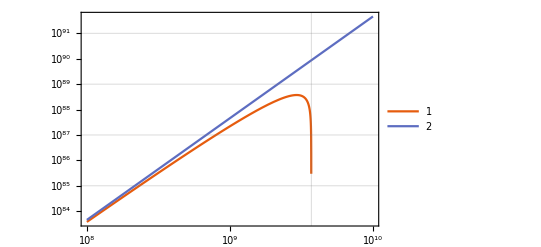

```mathematica
figasymp=LogLogPlot[{ργmodres[10.^9 TinGeV]/.{n0->n0ref,e1->e1ref},427/8 photonenergydensityboth[TinGeV gev]Quantity[("Centimeters")^3/("Electronvolts")]},{TinGeV,10.^8,10.^10},PlotLegends->Automatic,GridLines->{{3.702822896228357*^9},Automatic}]
```

```mathematica
Export["fig_asymp.pdf",figasymp]
```

fig_asymp.pdf

```mathematica
Solve[(ργmodres[10.^9 TinGeV]/.{n0->n0ref,e1->e1ref})/(427/8 photonenergydensityboth[TinGeV gev]Quantity[("Centimeters")^3/("Electronvolts")])==0.99,TinGeV]//ScientificForm
```

{{TinGeV→3.87517×10^5}}

```mathematica
√(387517.40988217987/(20. 10^-9))
```

4.4018×10^6

```mathematica
TinGeVOnePercent=Simplify[Solve[(ργmodres[10.^9 TinGeV])/(427/8 photonenergydensityboth[TinGeV gev]Quantity[("Centimeters")^3/("Electronvolts")])==0.99,TinGeV][[1,1,2]]]
```

3.7011×10^9 (0.000232461+(0.01 √(e1/e1ref) n0ref)/n0)^2.

```mathematica
TinGeVOnePercentMain=3.7011019749900403*^9 ((0.010000000000000222 √(e1/e1ref) n0ref)/n0)^2
```

(370110. e1 n0ref^2)/(e1ref n0^2)

```mathematica
jOnePercent=Assuming[n0ref>0&&n0>0,FullSimplify[√(TinGeVOnePercentMain/(20. 10^-9 e1/e1ref))]]
```

(4.3018×10^6 n0ref)/n0

## Construct the dmwel_data.data file

If all the calculations of data commented out above are done, the following creates the dmwel_data.data file

```mathematica
(*labels={"Histograms","Freezeout masses","CMB:parameters","CMB:chi","CMB:fc","CMB parameter ndm0","fForestell:en","fForestell:fgamma","fForestell:fe","Photodissociation cross sections","T_kd","Cut-off mass: free-streaming","Cut-off mass: damping","Cut-off mass: acoustic oscillation","f data","fSimp data"};data={sampledata,massfoTab,parameters,chiTable,fcTable,ndm0TabCMB,enArray,fγArray,feArray,{{σDpfnpre,σTDfnpre,σTnfnpre,σ3HeDfnpre,σ3Hepfnpre,σ4HeTfnpre,σ4He3Hefnpre,σ4HeDR1fnpre,σ4HeDR2fnpre,σ6Li4Hefnpre,σ6Li3Afnpre,σ7LiT4Hefnpre,σ7Li6Lifnpre,σ7Li4Hefnpre,σ7Be3He4Hefnpre,σ7Be6Lifnpre,σ7Be4Hefnpre},{σDpfnprelow,σTDfnprelow,σTnfnprelow,σ3HeDfnprelow,σ3Hepfnprelow,σ4HeTfnprelow,σ4He3Hefnprelow,σ4HeDR1fnprelow,σ4HeDR2fnprelow,σ6Li4Hefnprelow,σ6Li3Afnprelow,σ7LiT4Hefnprelow,σ7Li6Lifnprelow,σ7Li4Hefnprelow,σ7Be3He4Hefnprelow,σ7Be6Lifnprelow,σ7Be4Hefnprelow}},kdtab,cutOffMassfsTab,cutOffMassdTab,cutOffMassaoTab,fTab,fSimpTabF};dataFileExport["dmwel_data.data","Data for the DMWEL Mathematica notebook",labels,data]*)
```